```mathematica
(*Definição das novas coordenadas*)x={(R+r Cos[ψ]) Cos[ξ],(R+r Cos[ψ]) Sin[ξ],r Sin[ψ]};

(*Derivada em relação a ξ*)
gξ=D[x,ξ]//Simplify;
gξξ=gξ.gξ//Simplify;

(*Derivada em relação a r*)
gr=D[x,r]//Simplify;
grr=gr.gr//Simplify;

(*Vetores unitários em ξ e r*)
eξ=gξ/Sqrt[gξξ];
er=gr/Sqrt[grr];

(*Normal ao sistema*)
n=Simplify[Cross[eξ,er]];

(*Cálculo das velocidades angulares em ξ e r*)
ωξ=eξ.D[er,ξ]//Simplify;
ωr=er.D[eξ,r]//Simplify;

(*Cálculo das derivadas de gξ e gr*)
bξξ=n.D[gξ,ξ]//Simplify;
brbr=n.D[gr,r]//Simplify;

(*Cálculo das curvaturas*)
hξξ=bξξ/gξξ//Simplify;
hrhr=brbr/grr//Simplify;

(*Produtos de curvatura*)
G=hξξ hrhr//Simplify;
M=(hξξ+hrhr)/2//Simplify;
(*Cálculo de Omega e Gamma*)
Ω={ωξ/Sqrt[gξξ],ωr/Sqrt[grr]}//Simplify;
Γ={hξξ Cos[Φ[ψ,ξ]],hrhr Sin[Φ[ψ,ξ]]};

(*Derivada de Gamma*)
DΓ={-hξξ Sin[Φ[ψ,ξ]],hrhr Cos[Φ[ψ,ξ]]};
```

(Cos[ψ] (R+r Cos[ψ]))/(√((R+r Cos[ψ])^2))

0

```mathematica
(*GraTheta e GraPhi para ξ e r*)
Graξ={(1/Sqrt[gξξ]) D[Θ[ξ,r],ξ],(1/Sqrt[grr]) D[Θ[ξ,r],r]}

Grar={(1/Sqrt[gξξ]) D[Φ[ξ,r],ξ],(1/Sqrt[grr]) D[Φ[ξ,r],r]}

(*As propriedades a serem calculadas*)
Ex=(Graξ-Γ).(Graξ-Γ)+(Sin[Θ[ξ,r]] (Grar-Ω)-Cos[Θ[ξ,r]] D[Γ]).(Sin[Θ[ξ,r]] (Grar-Ω)-Cos[Θ[ξ,r]] D[Γ]);
```

{(Θ^(1,0)[ξ,r])/(√((R+r Cos[ψ])^2)),Θ^(0,1)[ξ,r]}

{(Φ^(1,0)[ξ,r])/(√((R+r Cos[ψ])^2)),Φ^(0,1)[ξ,r]}

PASSO 1: Parametrizacao do Cone (Eq. 9)

Vetor posicao r(chi,r) = {(1.+r/(√2)) Cos[chi],(1.+r/(√2)) Sin[chi],r/(√2)}

PASSO 2: Vetores da Base Tangente

e_chi (e1) = {(-1.-0.707107 r) Sin[chi],(1.+0.707107 r) Cos[chi],0}

e_r (e2) = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

g11 = 0.5 (2.+2.82843 r+r^2)

g22 = 1

g12 = 0 (deve ser 0 para base ortogonal)

e1 normalizado = {((-1.41421-1. r) Sin[chi])/(√(2.+2.82843 r+r^2)),((1.41421+1. r) Cos[chi])/(√(2.+2.82843 r+r^2)),0.}

e2 normalizado = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

PASSO 3: Vetor Normal

n = e1 x e2 = {((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2)),((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2)),(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))}

Verificar |n| = √(Abs[(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2))]^2) (deve ser 1)

PASSO 4: Segunda Forma Fundamental (curvatura)

b11 = -0.5 √(2.+2.82843 r+r^2)

b12 = 0

b21 = 0

b22 = 0

h11 = -(1. √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

h12 = 0.

h22 = 0

Curvatura de Gauss K = 0

Curvatura Media H = -(0.5 √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

PASSO 5: Spin Connection Omega

Omega_chi = varpi1/sqrt(g11) = (1.41421+1. r)/(2.+2.82843 r+r^2)

Omega_r = 0 (por simetria)

PASSO 6: Vetor Gamma(phi) - Eq. 4

Gamma_chi(phi) = -(1. Cos[phi])/(√(2.+2.82843 r+r^2))

Gamma_r(phi) = 0

PASSO 7: Campo Efetivo F_t(phi) - Eq. 5

F_t(phi, dphi/dchi) =

-(1. (dPhiDchi (-2.82843-4. r-1.41421 r^2)+1. (1.41421+1. r) √(2.+2.82843 r+r^2)) Sin[phi])/((2.+2.82843 r+r^2)^2)

PASSO 8: Solucao Onion phi_on(chi) - Eq. 11

Modulo k = 0.626647

Verificacao: 2*k*K(k^2) = 2.22144

pi*sin(psi) = 2.22144

PASSO 9: Calcular m_n/m_cn

PASSO 10: Plotagem

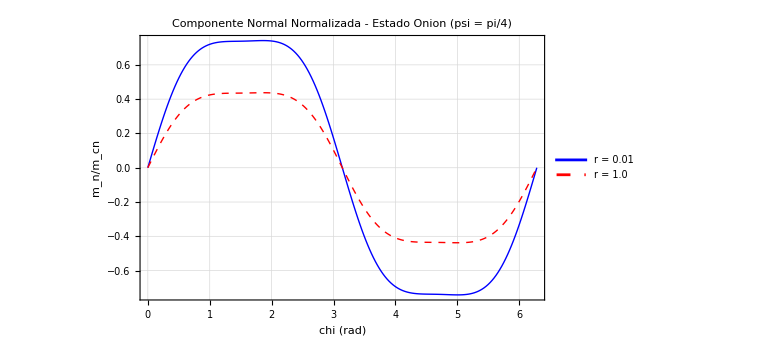

-Graphics-

Diagnostico:

m_cn (r=0.01): min = -0.741528, max = 0.741528

m_cn (r=1.0): min = -0.437449, max = 0.437449

```mathematica
(* =========================================*)(*ANALISE DA MAGNETIZACAO EM CONE-GAIDIDEI 2014*)(* =========================================*)(*PASSO 1:PARAMETRIZACAO DO CONE*)Print["PASSO 1: Parametrizacao do Cone (Eq. 9)"]

(*Coordenadas curvilineas*)
chi=Symbol["chi"]; (*angular:0 a 2pi*)
r=Symbol["r"];     (*radial:0 a w*)

(*Parametros do cone*)
R=1.0;             (*raio*)
psi=Pi/4;          (*angulo do cone*)

(*Parametrizacao:x+i*y=(R+r*cos(psi))*exp(i*chi),z=r*sin(psi)*)
xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi]
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi]
zCone[chi_,r_]:=r*Sin[psi]

(*Vetor posicao*)
rVec[chi_,r_]:={xCone[chi,r],yCone[chi,r],zCone[chi,r]}

Print["Vetor posicao r(chi,r) = ",rVec[chi,r]]

(* =========================================*)
(*PASSO 2:VETORES DA BASE TANGENTE*)
Print["\nPASSO 2: Vetores da Base Tangente"]

(*e_chi=dr/dchi*)
e1[chi_,r_]:=D[rVec[chi,r],chi]

(*e_r=dr/dr*)
e2[chi_,r_]:=D[rVec[chi,r],r]

Print["e_chi (e1) = ",e1[chi,r]//Simplify]
Print["e_r (e2) = ",e2[chi,r]//Simplify]

(*Componentes do tensor metrico*)
g11[chi_,r_]:=e1[chi,r].e1[chi,r]//Simplify
g22[chi_,r_]:=e2[chi,r].e2[chi,r]//Simplify
g12[chi_,r_]:=e1[chi,r].e2[chi,r]//Simplify

Print["g11 = ",g11[chi,r]]
Print["g22 = ",g22[chi,r]]
Print["g12 = ",g12[chi,r]," (deve ser 0 para base ortogonal)"]

(*Normalizar vetores da base*)
e1Norm[chi_,r_]:=e1[chi,r]/Sqrt[g11[chi,r]]
e2Norm[chi_,r_]:=e2[chi,r]/Sqrt[g22[chi,r]]

Print["e1 normalizado = ",e1Norm[chi,r]//Simplify]
Print["e2 normalizado = ",e2Norm[chi,r]//Simplify]

(* =========================================*)
(*PASSO 3:VETOR NORMAL*)
Print["\nPASSO 3: Vetor Normal"]

(*n=e1 x e2*)
nVec[chi_,r_]:=Cross[e1Norm[chi,r],e2Norm[chi,r]]//Simplify

Print["n = e1 x e2 = ",nVec[chi,r]]
Print["Verificar |n| = ",Norm[nVec[chi,r]]//Simplify," (deve ser 1)"]

(* =========================================*)
(*PASSO 4:SEGUNDA FORMA FUNDAMENTAL*)
Print["\nPASSO 4: Segunda Forma Fundamental (curvatura)"]

(*b_alphabeta=n.d(e_alpha)/d(xi_beta)*)
b11[chi_,r_]:=nVec[chi,r].D[e1[chi,r],chi]//Simplify
b12[chi_,r_]:=nVec[chi,r].D[e1[chi,r],r]//Simplify
b21[chi_,r_]:=nVec[chi,r].D[e2[chi,r],chi]//Simplify
b22[chi_,r_]:=nVec[chi,r].D[e2[chi,r],r]//Simplify

Print["b11 = ",b11[chi,r]]
Print["b12 = ",b12[chi,r]]
Print["b21 = ",b21[chi,r]]
Print["b22 = ",b22[chi,r]]

(*Matriz h_alphabeta=b_alphabeta/sqrt(g_alphaalpha*g_betabeta)*)
h11[chi_,r_]:=b11[chi,r]/Sqrt[g11[chi,r]*g11[chi,r]]//Simplify
h12[chi_,r_]:=b12[chi,r]/Sqrt[g11[chi,r]*g22[chi,r]]//Simplify
h22[chi_,r_]:=b22[chi,r]/Sqrt[g22[chi,r]*g22[chi,r]]//Simplify

Print["h11 = ",h11[chi,r]]
Print["h12 = ",h12[chi,r]]
Print["h22 = ",h22[chi,r]]

(*Curvatura de Gauss e curvatura media*)
K[chi_,r_]:=h11[chi,r]*h22[chi,r]-h12[chi,r]^2//Simplify
H[chi_,r_]:=(h11[chi,r]+h22[chi,r])/2//Simplify

Print["Curvatura de Gauss K = ",K[chi,r]]
Print["Curvatura Media H = ",H[chi,r]]

(* =========================================*)
(*PASSO 5:SPIN CONNECTION*)
Print["\nPASSO 5: Spin Connection Omega"]

(*varpi_1=e1.de2/dchi*)
varpi1[chi_,r_]:=e1Norm[chi,r].D[e2Norm[chi,r],chi]//Simplify

(*Omega=(varpi1/sqrt(g11),varpi2/sqrt(g22))*)
(*Para o cone,varpi2=0*)
Omega1[chi_,r_]:=varpi1[chi,r]/Sqrt[g11[chi,r]]//Simplify

Print["Omega_chi = varpi1/sqrt(g11) = ",Omega1[chi,r]]
Print["Omega_r = 0 (por simetria)"]

(* =========================================*)
(*PASSO 6:VETOR GAMMA (Eq.4)*)
Print["\nPASSO 6: Vetor Gamma(phi) - Eq. 4"]

(*Para o cone:Gamma=-e_chi*sin(psi)*cos(phi)/sqrt(g)*)
(*onde g=g11=(R+r*cos(psi))^2*)

phi=Symbol["phi"];
sqrtG[chi_,r_]:=Sqrt[g11[chi,r]]

GammaChi[phi_,chi_,r_]:=-Sin[psi]*Cos[phi]/sqrtG[chi,r]//Simplify
GammaR[phi_,chi_,r_]:=0

Print["Gamma_chi(phi) = ",GammaChi[phi,chi,r]]
Print["Gamma_r(phi) = ",GammaR[phi,chi,r]]

(* =========================================*)
(*PASSO 7:CAMPO EFETIVO F_t (Eq.5)*)
Print["\nPASSO 7: Campo Efetivo F_t(phi) - Eq. 5"]

(*F_t=div(Gamma)+(grad(phi)-Omega).(dGamma/dphi)*)

(*Divergencia de Gamma*)
divGamma[phi_,chi_,r_]:=Module[{sqrtg},sqrtg=Sqrt[g11[chi,r]*g22[chi,r]];
(1/sqrtg)*(D[GammaChi[phi,chi,r]*Sqrt[g11[chi,r]],chi]+D[GammaR[phi,chi,r]*Sqrt[g22[chi,r]],r])]//Simplify

(*grad(phi) em coordenadas curvilineas*)
gradPhiChi[chi_,r_]:=1/Sqrt[g11[chi,r]]
gradPhiR[chi_,r_]:=1/Sqrt[g22[chi,r]]

(*dGamma/dphi*)
dGammaDphi[phi_,chi_,r_]:=D[GammaChi[phi,chi,r],phi]//Simplify

(*F_t completo*)
Ft[phi_,dPhiDchi_,chi_,r_]:=Module[{term1,term2},term1=divGamma[phi,chi,r];
term2=(dPhiDchi*gradPhiChi[chi,r]-Omega1[chi,r])*dGammaDphi[phi,chi,r];
term1+term2]//Simplify

Print["F_t(phi, dphi/dchi) = "]
Print[Ft[phi,Symbol["dPhiDchi"],chi,r]]

(* =========================================*)
(*PASSO 8:SOLUCAO ONION phi(chi)*)
Print["\nPASSO 8: Solucao Onion phi_on(chi) - Eq. 11"]

(*Modulo k:2*k*K(k)=pi*sin(psi)*)
kEq=2*k*EllipticK[k^2]==Pi*Sin[psi];
kSol=FindRoot[kEq,{k,0.6}][[1,2]];

Print["Modulo k = ",kSol]
Print["Verificacao: 2*k*K(k^2) = ",2*kSol*EllipticK[kSol^2]//N]
Print["pi*sin(psi) = ",Pi*Sin[psi]//N]

(*Funcao phi_onion*)
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]

(* =========================================*)
(*PASSO 9:CALCULAR m_n/m_cn PARA PLOTAR*)
Print["\nPASSO 9: Calcular m_n/m_cn"]

(*Primeiro,criar funcao numerica para F_t*)
(*Simplificar F_t para o cone especificamente*)
FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Block[{gVal,result},gVal=(R+rVal*Cos[psi])^2;
result=Sin[psi]*Sin[phiVal]*(2*dPhiDchiVal-Cos[psi])/Sqrt[gVal];
result]

(*Valores numericos*)
nChi=200;
chiVals=Table[i,{i,0,2*Pi,2*Pi/nChi}];
rVals={0.01,1.0}; (*r=0 e r=R*)
sigma=0.15; (*parametro sigma*)

(*Calcular phi_onion para todos os chi*)
phiOnionVals=Table[phiOnion[chiVal],{chiVal,chiVals}];

(*Derivada numerica de phi*)
dPhiOnionVals=Table[If[i<Length[phiOnionVals],(phiOnionVals[[i+1]]-phiOnionVals[[i]])/(chiVals[[i+1]]-chiVals[[i]]),(phiOnionVals[[i]]-phiOnionVals[[i-1]])/(chiVals[[i]]-chiVals[[i-1]])],{i,1,Length[phiOnionVals]}];

(*Calcular m_cn para cada r*)
mcnData=Table[Table[{chiVals[[i]],R^2*FtCone[phiOnionVals[[i]],dPhiOnionVals[[i]],chiVals[[i]],rVal]},{i,1,Length[chiVals]}],{rVal,rVals}];

(* =========================================*)
(*PASSO 10:PLOTAR RESULTADOS*)
Print["\nPASSO 10: Plotagem"]

plot=ListLinePlot[mcnData,PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"r = 0.01","r = 1.0"},AxesLabel->{"chi (rad)","m_n/m_cn"},PlotLabel->"Componente Normal Normalizada - Estado Onion (psi = pi/4)",GridLines->Automatic,ImageSize->Large,Frame->True]

Print[plot]

(*Imprimir valores min/max para diagnostico*)
Print["\nDiagnostico:"]
Print["m_cn (r=0.01): min = ",Min[mcnData[[1,All,2]]],", max = ",Max[mcnData[[1,All,2]]]]
Print["m_cn (r=1.0): min = ",Min[mcnData[[2,All,2]]],", max = ",Max[mcnData[[2,All,2]]]]
```

```mathematica
(* =========================================*)(*ANALISE DA MAGNETIZACAO EM CONE-GAIDIDEI 2014*)(* =========================================*)(*PASSO 1:PARAMETRIZACAO DO CONE*)Print["PASSO 1: Parametrizacao do Cone (Eq. 9)"]

(*Coordenadas curvilineas*)
chi=Symbol["chi"]; (*angular:0 a 2pi*)
r=Symbol["r"];     (*radial:0 a w*)

(*Parametros do cone*)
R=1.0;             (*raio*)
psi=Pi/4;          (*angulo do cone*)

(*Parametrizacao:x+i*y=(R+r*cos(psi))*exp(i*chi),z=r*sin(psi)*)
xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi]
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi]
zCone[chi_,r_]:=r*Sin[psi]

(*Vetor posicao*)
rVec[chi_,r_]:={xCone[chi,r],yCone[chi,r],zCone[chi,r]}

Print["Vetor posicao r(chi,r) = ",rVec[chi,r]]

(* =========================================*)
(*PASSO 2:VETORES DA BASE TANGENTE*)
Print["\nPASSO 2: Vetores da Base Tangente"]

(*e_chi=dr/dchi*)
e1[chi_,r_]:=D[rVec[chi,r],chi]

(*e_r=dr/dr*)
e2[chi_,r_]:=D[rVec[chi,r],r]

Print["e_chi (e1) = ",e1[chi,r]//Simplify]
Print["e_r (e2) = ",e2[chi,r]//Simplify]

(*Componentes do tensor metrico*)
g11[chi_,r_]:=e1[chi,r].e1[chi,r]//Simplify
g22[chi_,r_]:=e2[chi,r].e2[chi,r]//Simplify
g12[chi_,r_]:=e1[chi,r].e2[chi,r]//Simplify

Print["g11 = ",g11[chi,r]]
Print["g22 = ",g22[chi,r]]
Print["g12 = ",g12[chi,r]," (deve ser 0 para base ortogonal)"]

(*Normalizar vetores da base*)
e1Norm[chi_,r_]:=e1[chi,r]/Sqrt[g11[chi,r]]
e2Norm[chi_,r_]:=e2[chi,r]/Sqrt[g22[chi,r]]

Print["e1 normalizado = ",e1Norm[chi,r]//Simplify]
Print["e2 normalizado = ",e2Norm[chi,r]//Simplify]

(* =========================================*)
(*PASSO 3:VETOR NORMAL*)
Print["\nPASSO 3: Vetor Normal"]

(*n=e1 x e2*)
nVec[chi_,r_]:=Cross[e1Norm[chi,r],e2Norm[chi,r]]//Simplify

Print["n = e1 x e2 = ",nVec[chi,r]]
Print["Verificar |n| = ",Norm[nVec[chi,r]]//Simplify," (deve ser 1)"]

(* =========================================*)
(*PASSO 4:SEGUNDA FORMA FUNDAMENTAL*)
Print["\nPASSO 4: Segunda Forma Fundamental (curvatura)"]

(*b_alphabeta=n.d(e_alpha)/d(xi_beta)*)
b11[chi_,r_]:=nVec[chi,r].D[e1[chi,r],chi]//Simplify
b12[chi_,r_]:=nVec[chi,r].D[e1[chi,r],r]//Simplify
b21[chi_,r_]:=nVec[chi,r].D[e2[chi,r],chi]//Simplify
b22[chi_,r_]:=nVec[chi,r].D[e2[chi,r],r]//Simplify

Print["b11 = ",b11[chi,r]]
Print["b12 = ",b12[chi,r]]
Print["b21 = ",b21[chi,r]]
Print["b22 = ",b22[chi,r]]

(*Matriz h_alphabeta=b_alphabeta/sqrt(g_alphaalpha*g_betabeta)*)
h11[chi_,r_]:=b11[chi,r]/Sqrt[g11[chi,r]*g11[chi,r]]//Simplify
h12[chi_,r_]:=b12[chi,r]/Sqrt[g11[chi,r]*g22[chi,r]]//Simplify
h22[chi_,r_]:=b22[chi,r]/Sqrt[g22[chi,r]*g22[chi,r]]//Simplify

Print["h11 = ",h11[chi,r]]
Print["h12 = ",h12[chi,r]]
Print["h22 = ",h22[chi,r]]

(*Curvatura de Gauss e curvatura media*)
K[chi_,r_]:=h11[chi,r]*h22[chi,r]-h12[chi,r]^2//Simplify
H[chi_,r_]:=(h11[chi,r]+h22[chi,r])/2//Simplify

Print["Curvatura de Gauss K = ",K[chi,r]]
Print["Curvatura Media H = ",H[chi,r]]

(* =========================================*)
(*PASSO 5:SPIN CONNECTION*)
Print["\nPASSO 5: Spin Connection Omega"]

(*varpi_1=e1.de2/dchi*)
varpi1[chi_,r_]:=e1Norm[chi,r].D[e2Norm[chi,r],chi]//Simplify

(*Omega=(varpi1/sqrt(g11),varpi2/sqrt(g22))*)
(*Para o cone,varpi2=0*)
Omega1[chi_,r_]:=varpi1[chi,r]/Sqrt[g11[chi,r]]//Simplify

Print["Omega_chi = varpi1/sqrt(g11) = ",Omega1[chi,r]]
Print["Omega_r = 0 (por simetria)"]

(* =========================================*)
(*PASSO 6:VETOR GAMMA (Eq.4)*)
Print["\nPASSO 6: Vetor Gamma(phi) - Eq. 4"]

(*Para o cone:Gamma=-e_chi*sin(psi)*cos(phi)/sqrt(g)*)
(*onde g=g11=(R+r*cos(psi))^2*)

phi=Symbol["phi"];
sqrtG[chi_,r_]:=Sqrt[g11[chi,r]]

GammaChi[phi_,chi_,r_]:=-Sin[psi]*Cos[phi]/sqrtG[chi,r]//Simplify
GammaR[phi_,chi_,r_]:=0

Print["Gamma_chi(phi) = ",GammaChi[phi,chi,r]]
Print["Gamma_r(phi) = ",GammaR[phi,chi,r]]

(* =========================================*)
(*PASSO 7:CAMPO EFETIVO F_t (Eq.5)*)
Print["\nPASSO 7: Campo Efetivo F_t(phi) - Eq. 5"]

(*F_t=div(Gamma)+(grad(phi)-Omega).(dGamma/dphi)*)

(*Divergencia de Gamma*)
divGamma[phi_,chi_,r_]:=Module[{sqrtg},sqrtg=Sqrt[g11[chi,r]*g22[chi,r]];
(1/sqrtg)*(D[GammaChi[phi,chi,r]*Sqrt[g11[chi,r]],chi]+D[GammaR[phi,chi,r]*Sqrt[g22[chi,r]],r])]//Simplify

(*grad(phi) em coordenadas curvilineas*)
gradPhiChi[chi_,r_]:=1/Sqrt[g11[chi,r]]
gradPhiR[chi_,r_]:=1/Sqrt[g22[chi,r]]

(*dGamma/dphi*)
dGammaDphi[phi_,chi_,r_]:=D[GammaChi[phi,chi,r],phi]//Simplify

(*F_t completo*)
Ft[phi_,dPhiDchi_,chi_,r_]:=Module[{term1,term2},term1=divGamma[phi,chi,r];
term2=(dPhiDchi*gradPhiChi[chi,r]-Omega1[chi,r])*dGammaDphi[phi,chi,r];
term1+term2]//Simplify

Print["F_t(phi, dphi/dchi) = "]
Print[Ft[phi,Symbol["dPhiDchi"],chi,r]]

(* =========================================*)
(*PASSO 8:SOLUCAO ONION phi(chi)*)
Print["\nPASSO 8: Solucao Onion phi_on(chi) - Eq. 11"]

(*Modulo k:2*k*K(k)=pi*sin(psi)*)
kEq=2*k*EllipticK[k^2]==Pi*Sin[psi];
kSol=FindRoot[kEq,{k,0.6}][[1,2]];

Print["Modulo k = ",kSol]
Print["Verificacao: 2*k*K(k^2) = ",2*kSol*EllipticK[kSol^2]//N]
Print["pi*sin(psi) = ",Pi*Sin[psi]//N]

(*Funcao phi_onion*)
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]

(* =========================================*)
(*PASSO 9:CALCULAR m_n/m_cn PARA PLOTAR*)
Print["\nPASSO 9: Calcular m_n/m_cn"]

(*Primeiro,criar funcao numerica para F_t*)
(*Simplificar F_t para o cone especificamente*)
FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Block[{gVal,result},gVal=(R+rVal*Cos[psi])^2;
result=Sin[psi]*Sin[phiVal]*(2*dPhiDchiVal-Cos[psi])/Sqrt[gVal];
result]

(*Valores numericos*)
nChi=200;
chiVals=Table[i,{i,0,2*Pi,2*Pi/nChi}];
rVals={0.01,1.0}; (*r=0 e r=R*)
sigma=0.15; (*parametro sigma*)

(*Calcular phi_onion para todos os chi*)
phiOnionVals=Table[phiOnion[chiVal],{chiVal,chiVals}];

(*Derivada numerica de phi*)
dPhiOnionVals=Table[If[i<Length[phiOnionVals],(phiOnionVals[[i+1]]-phiOnionVals[[i]])/(chiVals[[i+1]]-chiVals[[i]]),(phiOnionVals[[i]]-phiOnionVals[[i-1]])/(chiVals[[i]]-chiVals[[i-1]])],{i,1,Length[phiOnionVals]}];

(*Calcular m_cn para cada r*)
mcnData=Table[Table[{chiVals[[i]],R^2*FtCone[phiOnionVals[[i]],dPhiOnionVals[[i]],chiVals[[i]],rVal]},{i,1,Length[chiVals]}],{rVal,rVals}];

(* =========================================*)
(*PASSO 10:PLOTAR RESULTADOS*)
Print["\nPASSO 10: Plotagem"]

plot=ListLinePlot[mcnData,PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"r = 0.01","r = 1.0"},AxesLabel->{"chi (rad)","m_n/m_cn"},PlotLabel->"Componente Normal Normalizada - Estado Onion (psi = pi/4)",GridLines->Automatic,ImageSize->Large,Frame->True]

Print[plot]

(*Imprimir valores min/max para diagnostico*)
Print["\nDiagnostico:"]
Print["m_cn (r=0.01): min = ",Min[mcnData[[1,All,2]]],", max = ",Max[mcnData[[1,All,2]]]]
Print["m_cn (r=1.0): min = ",Min[mcnData[[2,All,2]]],", max = ",Max[mcnData[[2,All,2]]]]
```

PASSO 1: Parametrizacao do Cone (Eq. 9)

Vetor posicao r(chi,r) = {(1.+r/(√2)) Cos[chi],(1.+r/(√2)) Sin[chi],r/(√2)}

PASSO 2: Vetores da Base Tangente

e_chi (e1) = {(-1.-0.707107 r) Sin[chi],(1.+0.707107 r) Cos[chi],0}

e_r (e2) = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

g11 = 0.5 (2.+2.82843 r+r^2)

g22 = 1

g12 = 0 (deve ser 0 para base ortogonal)

e1 normalizado = {((-1.41421-1. r) Sin[chi])/(√(2.+2.82843 r+r^2)),((1.41421+1. r) Cos[chi])/(√(2.+2.82843 r+r^2)),0.}

e2 normalizado = {Cos[chi]/(√2),Sin[chi]/(√2),1/(√2)}

PASSO 3: Vetor Normal

n = e1 x e2 = {((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2)),((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2)),(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))}

Verificar |n| = √(Abs[(-1.-0.707107 r)/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Cos[chi])/(√(2.+2.82843 r+r^2))]^2+Abs[((1.+0.707107 r) Sin[chi])/(√(2.+2.82843 r+r^2))]^2) (deve ser 1)

PASSO 4: Segunda Forma Fundamental (curvatura)

b11 = -0.5 √(2.+2.82843 r+r^2)

b12 = 0

b21 = 0

b22 = 0

h11 = -(1. √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

h12 = 0.

h22 = 0

Curvatura de Gauss K = 0

Curvatura Media H = -(0.5 √(2.+2.82843 r+r^2))/(√((2.+2.82843 r+r^2)^2))

PASSO 5: Spin Connection Omega

Omega_chi = varpi1/sqrt(g11) = (1.41421+1. r)/(2.+2.82843 r+r^2)

Omega_r = 0 (por simetria)

PASSO 6: Vetor Gamma(phi) - Eq. 4

Gamma_chi(phi) = -(1. Cos[phi])/(√(2.+2.82843 r+r^2))

Gamma_r(phi) = 0

PASSO 7: Campo Efetivo F_t(phi) - Eq. 5

F_t(phi, dphi/dchi) =

-(1. (dPhiDchi (-2.82843-4. r-1.41421 r^2)+1. (1.41421+1. r) √(2.+2.82843 r+r^2)) Sin[phi])/((2.+2.82843 r+r^2)^2)

PASSO 8: Solucao Onion phi_on(chi) - Eq. 11

Modulo k = 0.626647

Verificacao: 2*k*K(k^2) = 2.22144

pi*sin(psi) = 2.22144

PASSO 9: Calcular m_n/m_cn

PASSO 10: Plotagem

-Graphics-

-Graphics-

Diagnostico:

m_cn (r=0.01): min = -0.741528, max = 0.741528

m_cn (r=1.0): min = -0.437449, max = 0.437449

Processando Painel B: ψ = 0...

Processando Painel C: ψ = π/4...

Processando Painel D: mn(χ)...

Processando Painel E: Plano de Corte...

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL D: mn(χ) ===

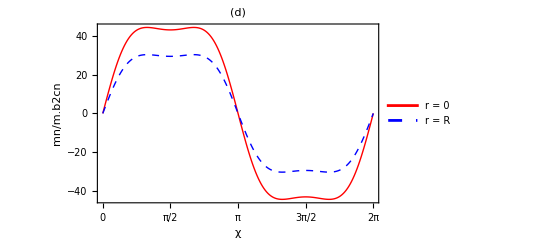

=== PAINEL E: Plano de Corte ===

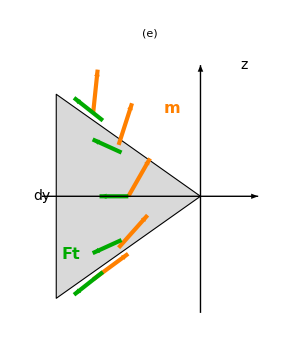

=== FIGURA 1 COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Sin[psi]*Sin[phiVal]*(2*dPhiDchiVal-Cos[psi])/Sqrt[(R+rVal*Cos[psi])^2];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
R^2*FtCone[phiVal,dPhiVal,chiVal,rVal]/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e vetor*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.1;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Thickness[0.006],Arrowheads[0.025],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["Processando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Thickness[0.006],Arrowheads[0.025],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)*)
(* =========================================*)

Print["Processando Painel D: mn(χ)..."];

mnDataD={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

plotD=ListLinePlot[mnDataD,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"r = 0","r = R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d)",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},All},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->400,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["Processando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Superfície do cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;(*ângulo típico*)angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*EXIBIR RESULTADOS*)
(* =========================================*)

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL D: mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo*)
finalFig=GraphicsGrid[{{plotB,plotC},{plotD,plotE}},ImageSize->850,Spacings->{40,40}];

Print["\n=== FIGURA 1 COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

Processando Painel C: ψ = π/4...

Processando Painel D: mn(χ)...

DEBUG - Teste phi_onion:

phi(0) = 0.

phi(π/2) = 1.5708

phi(π) = 3.14159

dphi/dchi(0) = 1.1284

dphi/dchi(π/2) = 0.879363

Ft(π/2, r=0.5) = 0.549374

DEBUG - Valores de mn:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

Processando Painel E: Plano de Corte...

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL D: mn(χ) ===

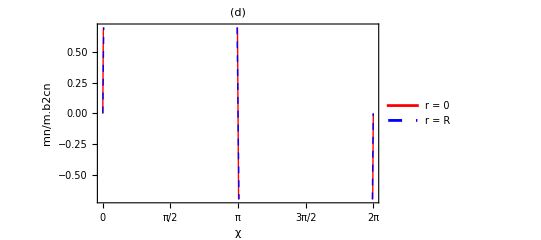

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA 1 COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
(*mn=R^2*Ft,normalizado por mcn*)R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
(*Retornar pontos para Arrow*){startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["Processando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)*)
(* =========================================*)

Print["Processando Painel D: mn(χ)..."];

(*Debug:Testar phi e derivada*)
Print["DEBUG - Teste phi_onion:"];
Print["  phi(0) = ",phiC[0]];
Print["  phi(π/2) = ",phiC[Pi/2]];
Print["  phi(π) = ",phiC[Pi]];
Print["  dphi/dchi(0) = ",Derivative[1][phiC][0]];
Print["  dphi/dchi(π/2) = ",Derivative[1][phiC][Pi/2]];

(*Testar Ft diretamente*)
testChi=Pi/2;
testR=0.5;
testPhi=phiC[testChi];
testDPhi=Derivative[1][phiC][testChi];
Print["  Ft(π/2, r=0.5) = ",Sin[Pi/4]*Sin[testPhi]*(2*testDPhi-Cos[Pi/4])/Sqrt[(R+testR*Cos[Pi/4])^2]];

mnDataD={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - Valores de mn:"];
Print["  r=0.05: Min = ",Min[mnDataD[[1,All,2]]],", Max = ",Max[mnDataD[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataD[[2,All,2]]],", Max = ",Max[mnDataD[[2,All,2]]]];

plotD=ListLinePlot[mnDataD,PlotStyle->{{Red,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"r = 0","r = R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d)",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->400,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["Processando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Superfície do cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;(*ângulo típico*)angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*EXIBIR RESULTADOS*)
(* =========================================*)

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL D: mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo*)
finalFig=GraphicsGrid[{{plotB,plotC},{plotD,plotE}},ImageSize->850,Spacings->{40,40}];

Print["\n=== FIGURA 1 COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

k = 0.

Processando Painel C: ψ = π/4...

k = 0.626647

Processando Painel C2: ψ = π/3...

k = 0.792726

Processando Painel D: mn(χ) para diferentes ψ...

DEBUG - ψ = π/4:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

DEBUG - ψ = π/3:

r=0.05: Min = -70.7199, Max = 70.7199

r=R: Min = -70.7199, Max = 70.7199

Processando Painel E: Plano de Corte...

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL C2: ψ = π/3 ===

-Graphics3D-

=== PAINEL D: Comparação mn(χ) ===

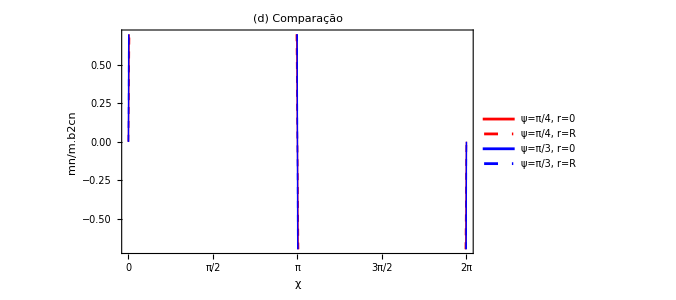

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/2];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*EXIBIR RESULTADOS*)
(* =========================================*)

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/3];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*CÁLCULO DA ENERGIA E_t*)
(* =========================================*)

Print["\n=== CÁLCULO DA ENERGIA E_t ==="];

(*Para o cone com ψ=π/4*)
psi=Pi/4;

(*Calcular E_t para diferentes valores de chi e r*)
CalculateEt[chi_,r_,phiVal_,dPhiDchi_]:=Module[{g11,g22,sqrtG,GammaChi,GammaR,Gamma2,gradPhiChi,gradPhiR,Omega1,Omega2,term1,term2,Et},(*Métrica*)g11=(R+r*Cos[psi])^2;
g22=1;
sqrtG=Sqrt[g11];
(*Componentes de Gamma (Eq.4)*)GammaChi=-Sin[psi]*Cos[phiVal]/sqrtG;
GammaR=0;
(*Gamma.b2*)Gamma2=GammaChi^2+GammaR^2;
(*Gradiente de phi em coordenadas curvilíneas*)gradPhiChi=dPhiDchi/Sqrt[g11];
gradPhiR=0;(*dphi/dr=0 para solução onion*)(*Spin connection Omega*)Omega1=-Sin[psi]/(R+r*Cos[psi]);
Omega2=0;
(*(∇φ-Ω).b2*)term1=(gradPhiChi-Omega1)^2;
term2=(gradPhiR-Omega2)^2;
(*Energia total*)Et=Gamma2+term1+term2;
{Et,Gamma2,term1+term2}];

(*Avaliar para alguns pontos*)
testPoints={{0,0.5},{Pi/2,0.5},{Pi,0.5},{0,0.1},{Pi/2,0.1}};

Print["\nEnergia E_t para ψ = π/4:"];
Print[StringForm["χ\t\tr\t\tE_t\t\tΓ.b2\t\t(∇φ-Ω).b2"]];
Print[StringRepeat["-",70]];

Do[Module[{chi,r,phiVal,dPhiVal,result},chi=testPoints[[i,1]];
r=testPoints[[i,2]];
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
Print[StringForm["``\t``\t``\t``\t``",N[chi,3],N[r,3],N[result[[1]],4],N[result[[2]],4],N[result[[3]],4]]]],{i,Length[testPoints]}];

(*Plotar E_t ao longo de chi*)
EtData=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,0.5,phiVal,dPhiVal];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/100}];

plotEt=ListLinePlot[EtData,PlotStyle->{Purple,Thick},Frame->True,FrameLabel->{Style["χ",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(χ) para ψ = π/4, r = 0.5",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

Print["\n=== GRÁFICO DE E_t ==="];
Print[plotEt];

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

k = 0.

Processando Painel C: ψ = π/4...

k = 0.626647

Processando Painel C2: ψ = π/3...

k = 0.724982

Processando Painel D: mn(χ) para diferentes ψ...

DEBUG - ψ = π/4:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

DEBUG - ψ = π/3:

r=0.05: Min = -44.2902, Max = 44.2902

r=R: Min = -30.265, Max = 30.265

Processando Painel E: Plano de Corte...

=== CÁLCULO DA ENERGIA E_t ===

Energia E_t para ψ = π/4 em diferentes r:

Avaliando em χ = π/2

----------------------------------------------------------------------

r		E_t		Γ.b2		(∇φ-Ω).b2

----------------------------------------------------------------------

0.1	2.19543	1.63526×10^-33	2.19543

0.3	1.71303	1.27594×10^-33	1.71303

0.5	1.37377	1.02325×10^-33	1.37377

0.7	1.12615	8.38811×10^-34	1.12615

0.9	0.939911	7.00092×10^-34	0.939911

=== GRÁFICO E_t(χ) PARA DIFERENTES r ===

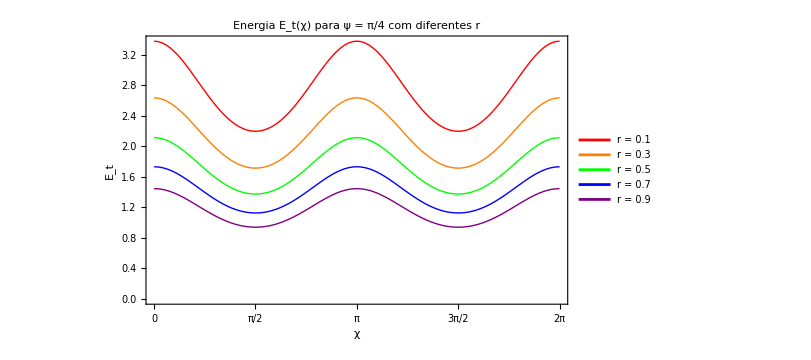

=== GRÁFICO E_t(r) PARA χ = π/2 ===

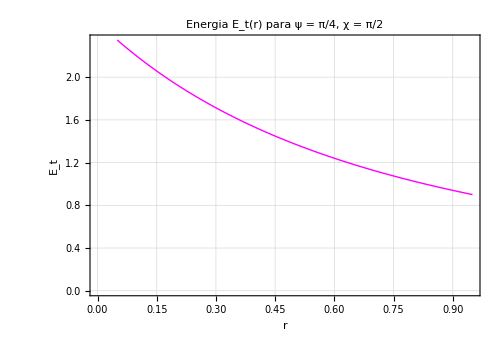

=== MAPA 2D DE E_t ===

-Graphics-

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL C2: ψ = π/3 ===

-Graphics3D-

=== PAINEL D: Comparação mn(χ) ===

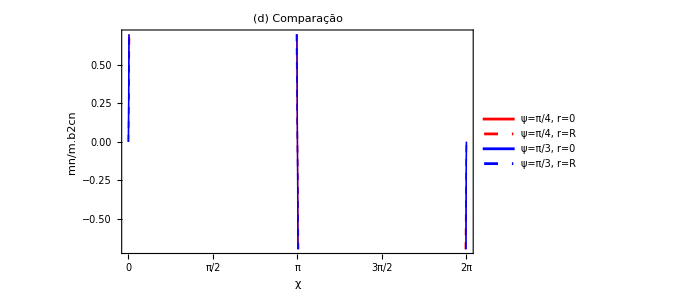

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/3];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*CÁLCULO DA ENERGIA E_t*)
(* =========================================*)

Print["\n=== CÁLCULO DA ENERGIA E_t ==="];

(*Para o cone com ψ=π/4*)
psi=Pi/4;

(*Calcular E_t para diferentes valores de chi e r*)
CalculateEt[chi_,r_,phiVal_,dPhiDchi_]:=Module[{g11,g22,sqrtG,GammaChi,GammaR,Gamma2,gradPhiChi,gradPhiR,Omega1,Omega2,term1,term2,Et},(*Métrica*)g11=(R+r*Cos[psi])^2;
g22=1;
sqrtG=Sqrt[g11];
(*Componentes de Gamma (Eq.4)*)GammaChi=-Sin[psi]*Cos[phiVal]/sqrtG;
GammaR=0;
(*Gamma.b2*)Gamma2=GammaChi^2+GammaR^2;
(*Gradiente de phi em coordenadas curvilíneas*)gradPhiChi=dPhiDchi/Sqrt[g11];
gradPhiR=0;(*dphi/dr=0 para solução onion*)(*Spin connection Omega*)Omega1=-Sin[psi]/(R+r*Cos[psi]);
Omega2=0;
(*(∇φ-Ω).b2*)term1=(gradPhiChi-Omega1)^2;
term2=(gradPhiR-Omega2)^2;
(*Energia total*)Et=Gamma2+term1+term2;
{Et,Gamma2,term1+term2}];

(*Valores de r para testar*)
rValues={0.1,0.3,0.5,0.7,0.9};

Print["\nEnergia E_t para ψ = π/4 em diferentes r:"];
Print["Avaliando em χ = π/2"];
Print[StringRepeat["-",70]];
Print[StringForm["r\t\tE_t\t\tΓ.b2\t\t(∇φ-Ω).b2"]];
Print[StringRepeat["-",70]];

Do[Module[{chi,r,phiVal,dPhiVal,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
Print[StringForm["``\t``\t``\t``",N[r,3],N[result[[1]],4],N[result[[2]],4],N[result[[3]],4]]]],{i,Length[rValues]}];

(*Plotar E_t ao longo de chi para diferentes r*)
EtDataMultiR=Table[Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,rVal,phiVal,dPhiVal];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/100}],{rVal,{0.1,0.3,0.5,0.7,0.9}}];

plotEtMultiR=ListLinePlot[EtDataMultiR,PlotStyle->{{Red,Thick},{Orange,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick}},PlotLegends->Placed[LineLegend[{"r = 0.1","r = 0.3","r = 0.5","r = 0.7","r = 0.9"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(χ) para ψ = π/4 com diferentes r",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

(*Plotar E_t em função de r para chi fixo*)
EtVsR=Table[Module[{chi,phiVal,dPhiVal,result},chi=Pi/2;
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
{r,result[[1]]}],{r,0.05,0.95,0.01}];

plotEtVsR=ListLinePlot[EtVsR,PlotStyle->{Magenta,Thick},Frame->True,FrameLabel->{Style["r",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(r) para ψ = π/4, χ = π/2",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

(*Mapa de densidade 2D:E_t(chi,r)*)
EtMap2D=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
result[[1]]],{chi,0,2*Pi,2*Pi/50},{r,0.05,0.95,0.02}];

plotEtMap=ListDensityPlot[Flatten[Table[{chi,r,EtMap2D[[i,j]]},{i,1,Length[EtMap2D]},{j,1,Length[EtMap2D[[1]]]}],1],ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,FrameLabel->{Style["χ",14],Style["r",14]},PlotLabel->Style["Mapa 2D: E_t(χ, r) para ψ = π/4",14,Bold],InterpolationOrder->2,ImageSize->500,AspectRatio->0.6];

Print["\n=== GRÁFICO E_t(χ) PARA DIFERENTES r ==="];
Print[plotEtMultiR];

Print["\n=== GRÁFICO E_t(r) PARA χ = π/2 ==="];
Print[plotEtVsR];

Print["\n=== MAPA 2D DE E_t ==="];
Print[plotEtMap];

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/3];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*CÁLCULO DA ENERGIA E_t*)
(* =========================================*)

Print["\n=== CÁLCULO DA ENERGIA E_t ==="];

(*Para o cone com ψ=π/4*)
psi=Pi/4;

(*Calcular E_t para diferentes valores de chi e r*)
CalculateEt[chi_,r_,phiVal_,dPhiDchi_]:=Module[{g11,g22,sqrtG,GammaChi,GammaR,Gamma2,gradPhiChi,gradPhiR,Omega1,Omega2,term1,term2,Et},(*Métrica*)g11=(R+r*Cos[psi])^2;
g22=1;
sqrtG=Sqrt[g11];
(*Componentes de Gamma (Eq.4)*)GammaChi=-Sin[psi]*Cos[phiVal]/sqrtG;
GammaR=0;
(*Gamma.b2*)Gamma2=GammaChi^2+GammaR^2;
(*Gradiente de phi em coordenadas curvilíneas*)(*Para solução geral,phi pode depender de r também*)gradPhiChi=dPhiDchi/Sqrt[g11];
gradPhiR=0/Sqrt[g22];(*Para onion puro,dphi/dr=0,mas mantemos termo geral*)(*Spin connection Omega*)Omega1=-Sin[psi]/(R+r*Cos[psi]);
Omega2=0;
(*(∇φ-Ω).b2*)term1=(gradPhiChi-Omega1)^2;
term2=(gradPhiR-Omega2)^2;
(*Energia total*)Et=Gamma2+term1+term2;
{Et,Gamma2,term1+term2}];

(*Valores de r para testar*)
rValues={0.1,0.3,0.5,0.7,0.9};

Print["\nEnergia E_t para ψ = π/4 em diferentes r:"];
Print["Avaliando em χ = π/2"];
Print[StringRepeat["-",70]];
Print[StringForm["r\t\tE_t\t\tΓ.b2\t\t(∇φ-Ω).b2"]];
Print[StringRepeat["-",70]];

Do[Module[{chi,r,phiVal,dPhiVal,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
Print[StringForm["``\t``\t``\t``",N[r,3],N[result[[1]],4],N[result[[2]],4],N[result[[3]],4]]]],{i,Length[rValues]}];

(*Plotar E_t ao longo de chi para diferentes r*)
EtDataMultiR=Table[Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,rVal,phiVal,dPhiVal];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/100}],{rVal,{0.1,0.3,0.5,0.7,0.9}}];

plotEtMultiR=ListLinePlot[EtDataMultiR,PlotStyle->{{Red,Thick},{Orange,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick}},PlotLegends->Placed[LineLegend[{"r = 0.1","r = 0.3","r = 0.5","r = 0.7","r = 0.9"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(χ) para ψ = π/4 com diferentes r",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

(*Plotar E_t em função de r para chi fixo*)
EtVsR=Table[Module[{chi,phiVal,dPhiVal,result},chi=Pi/2;
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
{r,result[[1]]}],{r,0.05,0.95,0.01}];

plotEtVsR=ListLinePlot[EtVsR,PlotStyle->{Magenta,Thick},Frame->True,FrameLabel->{Style["r",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(r) para ψ = π/4, χ = π/2",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

(*Mapa de densidade 2D:E_t(chi,r)*)
EtMap2D=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEt[chi,r,phiVal,dPhiVal];
result[[1]]],{chi,0,2*Pi,2*Pi/50},{r,0.05,0.95,0.02}];

plotEtMap=ListDensityPlot[Flatten[Table[{chi,r,EtMap2D[[i,j]]},{i,1,Length[EtMap2D]},{j,1,Length[EtMap2D[[1]]]}],1],ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,FrameLabel->{Style["χ",14],Style["r",14]},PlotLabel->Style["Mapa 2D: E_t(χ, r) para ψ = π/4",14,Bold],InterpolationOrder->2,ImageSize->500,AspectRatio->0.6];

Print["\n=== GRÁFICO E_t(χ) PARA DIFERENTES r ==="];
Print[plotEtMultiR];

Print["\n=== GRÁFICO E_t(r) PARA χ = π/2 ==="];
Print[plotEtVsR];

Print["\n=== MAPA 2D DE E_t ==="];
Print[plotEtMap];

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

k = 0.

Processando Painel C: ψ = π/4...

k = 0.626647

Processando Painel C2: ψ = π/3...

k = 0.724982

Processando Painel D: mn(χ) para diferentes ψ...

DEBUG - ψ = π/4:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

DEBUG - ψ = π/3:

r=0.05: Min = -44.2902, Max = 44.2902

r=R: Min = -30.265, Max = 30.265

Processando Painel E: Plano de Corte...

=== CÁLCULO DA ENERGIA E_t ===

Energia E_t para ψ = π/4 em diferentes r:

Avaliando em χ = π/2

----------------------------------------------------------------------

r		E_t		Γ.b2		(∇φ-Ω).b2

----------------------------------------------------------------------

0.1	2.19543	1.63526×10^-33	2.19543

0.3	1.71303	1.27594×10^-33	1.71303

0.5	1.37377	1.02325×10^-33	1.37377

0.7	1.12615	8.38811×10^-34	1.12615

0.9	0.939911	7.00092×10^-34	0.939911

=== GRÁFICO E_t(χ) PARA DIFERENTES r ===

-Graphics-

=== GRÁFICO E_t(r) PARA χ = π/2 ===

-Graphics-

=== MAPA 2D DE E_t ===

-Graphics-

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL C2: ψ = π/3 ===

-Graphics3D-

=== PAINEL D: Comparação mn(χ) ===

-Graphics-

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/3];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*CÁLCULO DA ENERGIA E_t-VERSÃO COMPLETA*)
(*E_t=Γ.b2+(∇φ-Ω).b2*)
(*Incluindo AMBOS os termos do gradiente*)
(* =========================================*)

Print["\n=== CÁLCULO COMPLETO DA ENERGIA E_t ==="];
Print["Desenvolvimento: E_t = Γ.b2 + (∇φ - Ω).b2"];
Print["onde (∇φ).b2 = (∂φ/∂χ).b2/g₁₁ + (∂φ/∂r).b2/g₂₂"];

(*Para o cone com ψ=π/4*)
psi=Pi/4;

(*Calcular E_t COMPLETO para diferentes valores de chi e r*)
CalculateEtComplete[chi_,r_,phiVal_,dPhiDchi_,dPhiDr_]:=Module[{g11,g22,sqrtG,GammaChi,GammaR,Gamma2,gradPhiChi,gradPhiR,gradPhiSq,Omega1,Omega2,OmegaSq,crossTerm,Et,termBreakdown},(*Métrica*)g11=(R+r*Cos[psi])^2;
g22=1;
sqrtG=Sqrt[g11];
(*Componentes de Gamma (Eq.4)*)GammaChi=-Sin[psi]*Cos[phiVal]/sqrtG;
GammaR=0;
Gamma2=GammaChi^2+GammaR^2;
(*Gradiente COMPLETO de phi*)gradPhiChi=dPhiDchi/Sqrt[g11];
gradPhiR=dPhiDr/Sqrt[g22];
gradPhiSq=gradPhiChi^2+gradPhiR^2;
(*Spin connection Omega*)Omega1=-Sin[psi]/(R+r*Cos[psi]);
Omega2=0;
OmegaSq=Omega1^2+Omega2^2;
(*Termo cruzado:-2(∇φ)·Ω*)crossTerm=-2*(gradPhiChi*Omega1+gradPhiR*Omega2);
(*Energia total:E_t=Γ.b2+(∇φ).b2-2(∇φ)·Ω+Ω.b2*)Et=Gamma2+gradPhiSq+crossTerm+OmegaSq;
(*Retornar com decomposição*)termBreakdown={{"Γ.b2",Gamma2},{"(∇φ).b2",gradPhiSq},{"  ├─ (∂φ/∂χ).b2/g₁₁",gradPhiChi^2},{"  └─ (∂φ/∂r).b2/g₂₂",gradPhiR^2},{"-2(∇φ)·Ω",crossTerm},{"Ω.b2",OmegaSq},{"E_t TOTAL",Et}};
{Et,termBreakdown}];

(*Para solução onion:dphi/dr=0*)
Print["\n=== CASO 1: Solução Onion (∂φ/∂r = 0) ==="];

rValues={0.1,0.3,0.5,0.7,0.9};

Print["\nEm χ = π/2:"];
Print[StringRepeat["=",80]];

Do[Module[{chi,r,phiVal,dPhiVal,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
Print["\nr = ",N[r,3]];
Print[StringRepeat["-",80]];
Do[Print[StringForm["  `` = ``",result[[2,j,1]],NumberForm[N[result[[2,j,2]],6],{6,4}]]],{j,Length[result[[2]]]}];],{i,Length[rValues]}];

(*CASO 2:Testar com derivada radial não-nula*)
Print["\n\n=== CASO 2: Com ∂φ/∂r ≠ 0 (exemplo hipotético) ==="];
Print["Testando: ∂φ/∂r = 0.1 sin(χ)"];

Do[Module[{chi,r,phiVal,dPhiDchi,dPhiDr,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiDchi=Derivative[1][phiC][chi];
dPhiDr=0.1*Sin[chi];(*Exemplo de dependência radial*)result=CalculateEtComplete[chi,r,phiVal,dPhiDchi,dPhiDr];
Print["\nr = ",N[r,3]];
Print[StringRepeat["-",80]];
Do[Print[StringForm["  `` = ``",result[[2,j,1]],NumberForm[N[result[[2,j,2]],6],{6,4}]]],{j,Length[result[[2]]]}];],{i,Length[rValues]}];

(*Plotar E_t ao longo de chi para diferentes r-VERSÃO CORRIGIDA*)
EtDataMultiR=Table[Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,rVal,phiVal,dPhiVal,0];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/100}],{rVal,{0.1,0.3,0.5,0.7,0.9}}];

plotEtMultiR=ListLinePlot[EtDataMultiR,PlotStyle->{{Red,Thick},{Orange,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick}},PlotLegends->Placed[LineLegend[{"r = 0.1","r = 0.3","r = 0.5","r = 0.7","r = 0.9"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(χ) para ψ = π/4 com diferentes r",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

(*Plotar E_t em função de r para chi fixo-VERSÃO CORRIGIDA*)
EtVsR=Table[Module[{chi,phiVal,dPhiVal,result},chi=Pi/2;
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
{r,result[[1]]}],{r,0.05,0.95,0.01}];

plotEtVsR=ListLinePlot[EtVsR,PlotStyle->{Magenta,Thick},Frame->True,FrameLabel->{Style["r",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(r) para ψ = π/4, χ = π/2",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

(*Mapa de densidade 2D:E_t(chi,r)-VERSÃO CORRIGIDA*)
EtMap2D=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
result[[1]]],{chi,0,2*Pi,2*Pi/50},{r,0.05,0.95,0.02}];

plotEtMap=ListDensityPlot[Flatten[Table[{chi,r,EtMap2D[[i,j]]},{i,1,Length[EtMap2D]},{j,1,Length[EtMap2D[[1]]]}],1],ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,FrameLabel->{Style["χ",14],Style["r",14]},PlotLabel->Style["Mapa 2D: E_t(χ, r) para ψ = π/4",14,Bold],InterpolationOrder->2,ImageSize->500,AspectRatio->0.6];

Print["\n=== GRÁFICO E_t(χ) PARA DIFERENTES r ==="];
Print[plotEtMultiR];

Print["\n=== GRÁFICO E_t(r) PARA χ = π/2 ==="];
Print[plotEtVsR];

Print["\n=== MAPA 2D DE E_t ==="];
Print[plotEtMap];

(* =========================================*)
(*IDENTIFICAR PONTOS CRÍTICOS DE ENERGIA*)
(* =========================================*)

Print["\n=== IDENTIFICAÇÃO DE PONTOS CRÍTICOS ==="];

(*Encontrar mínimos e máximos em função de chi para r fixo*)
rTest=0.5;
EtProfile=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,rTest,phiVal,dPhiVal,0];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/200}];

(*Encontrar posições de mínimos e máximos*)
etValues=EtProfile[[All,2]];
chiValues=EtProfile[[All,1]];

(*Buscar extremos locais*)
criticalPoints={};
Do[If[i>1&&i<Length[etValues],Module[{prev,curr,next},prev=etValues[[i-1]];
curr=etValues[[i]];
next=etValues[[i+1]];
(*Máximo local*)If[curr>prev&&curr>next,AppendTo[criticalPoints,{chiValues[[i]],curr,"Máximo"}]];
(*Mínimo local*)If[curr<prev&&curr<next,AppendTo[criticalPoints,{chiValues[[i]],curr,"Mínimo"}]];]],{i,2,Length[etValues]-1}];

Print["\nPontos críticos encontrados para r = ",rTest,":"];
Print[StringRepeat["=",80]];
Do[Print[StringForm["`` em χ = `` rad (``°), E_t = ``",criticalPoints[[i,3]],NumberForm[criticalPoints[[i,1]],{4,3}],NumberForm[criticalPoints[[i,1]]*180/Pi,{5,1}],NumberForm[criticalPoints[[i,2]],{6,4}]]],{i,Length[criticalPoints]}];

(*Converter para coordenadas 3D*)
criticalPoints3D=Table[Module[{chi,Et,tipo,x,y,z},chi=criticalPoints[[i,1]];
Et=criticalPoints[[i,2]];
tipo=criticalPoints[[i,3]];
x=xC[chi,rTest];
y=yC[chi,rTest];
z=zC[chi,rTest];
{{x,y,z},tipo,Et}],{i,Length[criticalPoints]}];

Print["\nCoordenadas 3D dos pontos críticos:"];
Do[Print[StringForm["`` em (x, y, z) = (`` , `` , ``), E_t = ``",criticalPoints3D[[i,2]],NumberForm[criticalPoints3D[[i,1,1]],{4,3}],NumberForm[criticalPoints3D[[i,1,2]],{4,3}],NumberForm[criticalPoints3D[[i,1,3]],{4,3}],NumberForm[criticalPoints3D[[i,3]],{6,4}]]],{i,Length[criticalPoints3D]}];

(*Plotar cone com pontos críticos marcados*)
plotConeWithCritical=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->True,AxesLabel->{"x","y","z"}],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],(*Marcar mínimos em VERDE*)Graphics3D[{Green,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Mínimo"&]],(*Marcar máximos em VERMELHO*)Graphics3D[{Red,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Máximo"&]],(*Adicionar labels*)Graphics3D[Table[Text[Style[criticalPoints3D[[i,2]],12,Bold,If[criticalPoints3D[[i,2]]=="Mínimo",Green,Red]],criticalPoints3D[[i,1]]+{0,0,0.15}],{i,Length[criticalPoints3D]}]],ViewPoint->{2.5,-2,1.5},ImageSize->600,PlotLabel->Style["Cone com Pontos Críticos de Energia (ψ = π/4, r = 0.5)",14,Bold]];

Print["\n=== CONE 3D COM PONTOS CRÍTICOS MARCADOS ==="];
Print[plotConeWithCritical];

(*Plotar vista superior para melhor visualização*)
plotTopView=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->True],Graphics3D[{Green,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Mínimo"&]],Graphics3D[{Red,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Máximo"&]],ViewPoint->{0,0,3},ImageSize->500,PlotLabel->Style["Vista Superior - Pontos Críticos",14,Bold]];

Print["\n=== VISTA SUPERIOR ==="];
Print[plotTopView];

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

k = 0.

Processando Painel C: ψ = π/4...

k = 0.626647

Processando Painel C2: ψ = π/3...

k = 0.724982

Processando Painel D: mn(χ) para diferentes ψ...

DEBUG - ψ = π/4:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

DEBUG - ψ = π/3:

r=0.05: Min = -44.2902, Max = 44.2902

r=R: Min = -30.265, Max = 30.265

Processando Painel E: Plano de Corte...

=== CÁLCULO COMPLETO DA ENERGIA E_t ===

Desenvolvimento: E_t = Γ.b2 + (∇φ - Ω).b2

onde (∇φ).b2 = (∂φ/∂χ).b2/g₁₁ + (∂φ/∂r).b2/g₂₂

=== CASO 1: Solução Onion (∂φ/∂r = 0) ===

Em χ = π/2:

================================================================================

r = 0.1

--------------------------------------------------------------------------------

Γ.b2 = 1.6353×10^-33

(∇φ).b2 = 0.6745

├─ (∂φ/∂χ).b2/g₁₁ = 0.6745

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 1.0848

Ω.b2 = 0.4361

E_t TOTAL = 2.1954

r = 0.3

--------------------------------------------------------------------------------

Γ.b2 = 1.2759×10^-33

(∇φ).b2 = 0.5263

├─ (∂φ/∂χ).b2/g₁₁ = 0.5263

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.8464

Ω.b2 = 0.3403

E_t TOTAL = 1.7130

r = 0.5

--------------------------------------------------------------------------------

Γ.b2 = 1.0232×10^-33

(∇φ).b2 = 0.4221

├─ (∂φ/∂χ).b2/g₁₁ = 0.4221

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.6788

Ω.b2 = 0.2729

E_t TOTAL = 1.3738

r = 0.7

--------------------------------------------------------------------------------

Γ.b2 = 8.3881×10^-34

(∇φ).b2 = 0.3460

├─ (∂φ/∂χ).b2/g₁₁ = 0.3460

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.5564

Ω.b2 = 0.2237

E_t TOTAL = 1.1261

r = 0.9

--------------------------------------------------------------------------------

Γ.b2 = 7.0009×10^-34

(∇φ).b2 = 0.2888

├─ (∂φ/∂χ).b2/g₁₁ = 0.2888

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.4644

Ω.b2 = 0.1867

E_t TOTAL = 0.9399

=== CASO 2: Com ∂φ/∂r ≠ 0 (exemplo hipotético) ===

Testando: ∂φ/∂r = 0.1 sin(χ)

r = 0.1

--------------------------------------------------------------------------------

Γ.b2 = 1.6353×10^-33

(∇φ).b2 = 0.6845

├─ (∂φ/∂χ).b2/g₁₁ = 0.6745

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 1.0848

Ω.b2 = 0.4361

E_t TOTAL = 2.2054

r = 0.3

--------------------------------------------------------------------------------

Γ.b2 = 1.2759×10^-33

(∇φ).b2 = 0.5363

├─ (∂φ/∂χ).b2/g₁₁ = 0.5263

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.8464

Ω.b2 = 0.3403

E_t TOTAL = 1.7230

r = 0.5

--------------------------------------------------------------------------------

Γ.b2 = 1.0232×10^-33

(∇φ).b2 = 0.4321

├─ (∂φ/∂χ).b2/g₁₁ = 0.4221

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.6788

Ω.b2 = 0.2729

E_t TOTAL = 1.3838

r = 0.7

--------------------------------------------------------------------------------

Γ.b2 = 8.3881×10^-34

(∇φ).b2 = 0.3560

├─ (∂φ/∂χ).b2/g₁₁ = 0.3460

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.5564

Ω.b2 = 0.2237

E_t TOTAL = 1.1361

r = 0.9

--------------------------------------------------------------------------------

Γ.b2 = 7.0009×10^-34

(∇φ).b2 = 0.2988

├─ (∂φ/∂χ).b2/g₁₁ = 0.2888

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.4644

Ω.b2 = 0.1867

E_t TOTAL = 0.9499

=== GRÁFICO E_t(χ) PARA DIFERENTES r ===

-Graphics-

=== GRÁFICO E_t(r) PARA χ = π/2 ===

-Graphics-

=== MAPA 2D DE E_t ===

-Graphics-

=== IDENTIFICAÇÃO DE PONTOS CRÍTICOS ===

Pontos críticos encontrados para r = 0.5:

================================================================================

Mínimo em χ = π/2 rad (90°), E_t = 1.3738

Máximo em χ = π rad (180°), E_t = 2.1118

Mínimo em χ = (3 π)/2 rad (270°), E_t = 1.3738

Coordenadas 3D dos pontos críticos:

Mínimo em (x, y, z) = (0.000 , 1.354 , 0.354), E_t = 1.3738

Máximo em (x, y, z) = (-1.354 , 0.000 , 0.354), E_t = 2.1118

Mínimo em (x, y, z) = (0.000 , -1.354 , 0.354), E_t = 1.3738

=== CONE 3D COM PONTOS CRÍTICOS MARCADOS ===

-Graphics3D-

=== VISTA SUPERIOR ===

-Graphics3D-

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL C2: ψ = π/3 ===

-Graphics3D-

=== PAINEL D: Comparação mn(χ) ===

-Graphics-

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA COMPLETA ===

-Graphics-

Processando Painel B: ψ = 0...

k = 0.

Processando Painel C: ψ = π/4...

k = 0.626647

Processando Painel C2: ψ = π/3...

k = 0.724982

Processando Painel D: mn(χ) para diferentes ψ...

DEBUG - ψ = π/4:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

DEBUG - ψ = π/3:

r=0.05: Min = -44.2902, Max = 44.2902

r=R: Min = -30.265, Max = 30.265

Processando Painel E: Plano de Corte...

=== CÁLCULO COMPLETO DA ENERGIA E_t ===

Desenvolvimento: E_t = Γ.b2 + (∇φ - Ω).b2

onde (∇φ).b2 = (∂φ/∂χ).b2/g₁₁ + (∂φ/∂r).b2/g₂₂

=== CASO 1: Solução Onion (∂φ/∂r = 0) ===

Em χ = π/2:

================================================================================

r = 0.1

--------------------------------------------------------------------------------

Γ.b2 = 1.6353×10^-33

(∇φ).b2 = 0.6745

├─ (∂φ/∂χ).b2/g₁₁ = 0.6745

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 1.0848

Ω.b2 = 0.4361

E_t TOTAL = 2.1954

r = 0.3

--------------------------------------------------------------------------------

Γ.b2 = 1.2759×10^-33

(∇φ).b2 = 0.5263

├─ (∂φ/∂χ).b2/g₁₁ = 0.5263

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.8464

Ω.b2 = 0.3403

E_t TOTAL = 1.7130

r = 0.5

--------------------------------------------------------------------------------

Γ.b2 = 1.0232×10^-33

(∇φ).b2 = 0.4221

├─ (∂φ/∂χ).b2/g₁₁ = 0.4221

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.6788

Ω.b2 = 0.2729

E_t TOTAL = 1.3738

r = 0.7

--------------------------------------------------------------------------------

Γ.b2 = 8.3881×10^-34

(∇φ).b2 = 0.3460

├─ (∂φ/∂χ).b2/g₁₁ = 0.3460

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.5564

Ω.b2 = 0.2237

E_t TOTAL = 1.1261

r = 0.9

--------------------------------------------------------------------------------

Γ.b2 = 7.0009×10^-34

(∇φ).b2 = 0.2888

├─ (∂φ/∂χ).b2/g₁₁ = 0.2888

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.4644

Ω.b2 = 0.1867

E_t TOTAL = 0.9399

=== CASO 2: Com ∂φ/∂r ≠ 0 (exemplo hipotético) ===

Testando: ∂φ/∂r = 0.1 sin(χ)

r = 0.1

--------------------------------------------------------------------------------

Γ.b2 = 1.6353×10^-33

(∇φ).b2 = 0.6845

├─ (∂φ/∂χ).b2/g₁₁ = 0.6745

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 1.0848

Ω.b2 = 0.4361

E_t TOTAL = 2.2054

r = 0.3

--------------------------------------------------------------------------------

Γ.b2 = 1.2759×10^-33

(∇φ).b2 = 0.5363

├─ (∂φ/∂χ).b2/g₁₁ = 0.5263

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.8464

Ω.b2 = 0.3403

E_t TOTAL = 1.7230

r = 0.5

--------------------------------------------------------------------------------

Γ.b2 = 1.0232×10^-33

(∇φ).b2 = 0.4321

├─ (∂φ/∂χ).b2/g₁₁ = 0.4221

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.6788

Ω.b2 = 0.2729

E_t TOTAL = 1.3838

r = 0.7

--------------------------------------------------------------------------------

Γ.b2 = 8.3881×10^-34

(∇φ).b2 = 0.3560

├─ (∂φ/∂χ).b2/g₁₁ = 0.3460

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.5564

Ω.b2 = 0.2237

E_t TOTAL = 1.1361

r = 0.9

--------------------------------------------------------------------------------

Γ.b2 = 7.0009×10^-34

(∇φ).b2 = 0.2988

├─ (∂φ/∂χ).b2/g₁₁ = 0.2888

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.4644

Ω.b2 = 0.1867

E_t TOTAL = 0.9499

=== GRÁFICO E_t(χ) PARA DIFERENTES r ===

-Graphics-

=== GRÁFICO E_t(r) PARA χ = π/2 ===

-Graphics-

=== MAPA 2D DE E_t ===

-Graphics-

=== IDENTIFICAÇÃO DE PONTOS CRÍTICOS ===

Pontos críticos encontrados para r = 0.5:

================================================================================

Mínimo em χ = π/2 rad (90°), E_t = 1.3738

Máximo em χ = π rad (180°), E_t = 2.1118

Mínimo em χ = (3 π)/2 rad (270°), E_t = 1.3738

Coordenadas 3D dos pontos críticos:

Mínimo em (x, y, z) = (0.000 , 1.354 , 0.354), E_t = 1.3738

Máximo em (x, y, z) = (-1.354 , 0.000 , 0.354), E_t = 2.1118

Mínimo em (x, y, z) = (0.000 , -1.354 , 0.354), E_t = 1.3738

=== CONE 3D COM PONTOS CRÍTICOS MARCADOS ===

-Graphics3D-

=== VISTA SUPERIOR ===

-Graphics3D-

=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ===

Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0

=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ===

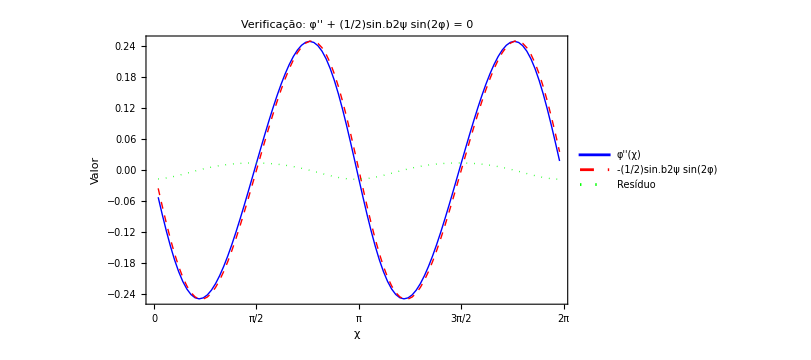

Estatísticas do Resíduo:

RMS = 0.0110493

Max|resíduo| = 0.0176921

(Valores próximos de zero indicam solução correta)

=== RESOLVER EQUAÇÃO DO PÊNDULO NUMERICAMENTE ===

Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0

Condições: φ(0) = 0, φ'(0) ≈ 1 (ajustado para periodicidade)

=== COMPARAÇÃO: ONION vs NUMÉRICO ===

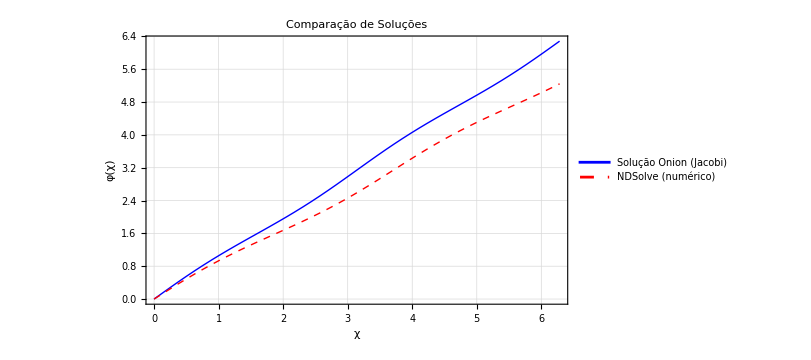

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL C2: ψ = π/3 ===

-Graphics3D-

=== PAINEL D: Comparação mn(χ) ===

-Graphics-

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/3];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*CÁLCULO DA ENERGIA E_t-VERSÃO COMPLETA*)
(*E_t=Γ.b2+(∇φ-Ω).b2*)
(*Incluindo AMBOS os termos do gradiente*)
(* =========================================*)

Print["\n=== CÁLCULO COMPLETO DA ENERGIA E_t ==="];
Print["Desenvolvimento: E_t = Γ.b2 + (∇φ - Ω).b2"];
Print["onde (∇φ).b2 = (∂φ/∂χ).b2/g₁₁ + (∂φ/∂r).b2/g₂₂"];

(*Para o cone com ψ=π/4*)
psi=Pi/4;

(*Calcular E_t COMPLETO para diferentes valores de chi e r*)
CalculateEtComplete[chi_,r_,phiVal_,dPhiDchi_,dPhiDr_]:=Module[{g11,g22,sqrtG,GammaChi,GammaR,Gamma2,gradPhiChi,gradPhiR,gradPhiSq,Omega1,Omega2,OmegaSq,crossTerm,Et,termBreakdown},(*Métrica*)g11=(R+r*Cos[psi])^2;
g22=1;
sqrtG=Sqrt[g11];
(*Componentes de Gamma (Eq.4)*)GammaChi=-Sin[psi]*Cos[phiVal]/sqrtG;
GammaR=0;
Gamma2=GammaChi^2+GammaR^2;
(*Gradiente COMPLETO de phi*)gradPhiChi=dPhiDchi/Sqrt[g11];
gradPhiR=dPhiDr/Sqrt[g22];
gradPhiSq=gradPhiChi^2+gradPhiR^2;
(*Spin connection Omega*)Omega1=-Sin[psi]/(R+r*Cos[psi]);
Omega2=0;
OmegaSq=Omega1^2+Omega2^2;
(*Termo cruzado:-2(∇φ)·Ω*)crossTerm=-2*(gradPhiChi*Omega1+gradPhiR*Omega2);
(*Energia total:E_t=Γ.b2+(∇φ).b2-2(∇φ)·Ω+Ω.b2*)Et=Gamma2+gradPhiSq+crossTerm+OmegaSq;
(*Retornar com decomposição*)termBreakdown={{"Γ.b2",Gamma2},{"(∇φ).b2",gradPhiSq},{"  ├─ (∂φ/∂χ).b2/g₁₁",gradPhiChi^2},{"  └─ (∂φ/∂r).b2/g₂₂",gradPhiR^2},{"-2(∇φ)·Ω",crossTerm},{"Ω.b2",OmegaSq},{"E_t TOTAL",Et}};
{Et,termBreakdown}];

(*Para solução onion:dphi/dr=0*)
Print["\n=== CASO 1: Solução Onion (∂φ/∂r = 0) ==="];

rValues={0.1,0.3,0.5,0.7,0.9};

Print["\nEm χ = π/2:"];
Print[StringRepeat["=",80]];

Do[Module[{chi,r,phiVal,dPhiVal,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
Print["\nr = ",N[r,3]];
Print[StringRepeat["-",80]];
Do[Print[StringForm["  `` = ``",result[[2,j,1]],NumberForm[N[result[[2,j,2]],6],{6,4}]]],{j,Length[result[[2]]]}];],{i,Length[rValues]}];

(*CASO 2:Testar com derivada radial não-nula*)
Print["\n\n=== CASO 2: Com ∂φ/∂r ≠ 0 (exemplo hipotético) ==="];
Print["Testando: ∂φ/∂r = 0.1 sin(χ)"];

Do[Module[{chi,r,phiVal,dPhiDchi,dPhiDr,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiDchi=Derivative[1][phiC][chi];
dPhiDr=0.1*Sin[chi];(*Exemplo de dependência radial*)result=CalculateEtComplete[chi,r,phiVal,dPhiDchi,dPhiDr];
Print["\nr = ",N[r,3]];
Print[StringRepeat["-",80]];
Do[Print[StringForm["  `` = ``",result[[2,j,1]],NumberForm[N[result[[2,j,2]],6],{6,4}]]],{j,Length[result[[2]]]}];],{i,Length[rValues]}];

(*Plotar E_t ao longo de chi para diferentes r-VERSÃO CORRIGIDA*)
EtDataMultiR=Table[Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,rVal,phiVal,dPhiVal,0];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/100}],{rVal,{0.1,0.3,0.5,0.7,0.9}}];

plotEtMultiR=ListLinePlot[EtDataMultiR,PlotStyle->{{Red,Thick},{Orange,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick}},PlotLegends->Placed[LineLegend[{"r = 0.1","r = 0.3","r = 0.5","r = 0.7","r = 0.9"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(χ) para ψ = π/4 com diferentes r",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

(*Plotar E_t em função de r para chi fixo-VERSÃO CORRIGIDA*)
EtVsR=Table[Module[{chi,phiVal,dPhiVal,result},chi=Pi/2;
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
{r,result[[1]]}],{r,0.05,0.95,0.01}];

plotEtVsR=ListLinePlot[EtVsR,PlotStyle->{Magenta,Thick},Frame->True,FrameLabel->{Style["r",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(r) para ψ = π/4, χ = π/2",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

(*Mapa de densidade 2D:E_t(chi,r)-VERSÃO CORRIGIDA*)
EtMap2D=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
result[[1]]],{chi,0,2*Pi,2*Pi/50},{r,0.05,0.95,0.02}];

plotEtMap=ListDensityPlot[Flatten[Table[{chi,r,EtMap2D[[i,j]]},{i,1,Length[EtMap2D]},{j,1,Length[EtMap2D[[1]]]}],1],ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,FrameLabel->{Style["χ",14],Style["r",14]},PlotLabel->Style["Mapa 2D: E_t(χ, r) para ψ = π/4",14,Bold],InterpolationOrder->2,ImageSize->500,AspectRatio->0.6];

Print["\n=== GRÁFICO E_t(χ) PARA DIFERENTES r ==="];
Print[plotEtMultiR];

Print["\n=== GRÁFICO E_t(r) PARA χ = π/2 ==="];
Print[plotEtVsR];

Print["\n=== MAPA 2D DE E_t ==="];
Print[plotEtMap];

(* =========================================*)
(*IDENTIFICAR PONTOS CRÍTICOS DE ENERGIA*)
(* =========================================*)

Print["\n=== IDENTIFICAÇÃO DE PONTOS CRÍTICOS ==="];

(*Encontrar mínimos e máximos em função de chi para r fixo*)
rTest=0.5;
EtProfile=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,rTest,phiVal,dPhiVal,0];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/200}];

(*Encontrar posições de mínimos e máximos*)
etValues=EtProfile[[All,2]];
chiValues=EtProfile[[All,1]];

(*Buscar extremos locais*)
criticalPoints={};
Do[If[i>1&&i<Length[etValues],Module[{prev,curr,next},prev=etValues[[i-1]];
curr=etValues[[i]];
next=etValues[[i+1]];
(*Máximo local*)If[curr>prev&&curr>next,AppendTo[criticalPoints,{chiValues[[i]],curr,"Máximo"}]];
(*Mínimo local*)If[curr<prev&&curr<next,AppendTo[criticalPoints,{chiValues[[i]],curr,"Mínimo"}]];]],{i,2,Length[etValues]-1}];

Print["\nPontos críticos encontrados para r = ",rTest,":"];
Print[StringRepeat["=",80]];
Do[Print[StringForm["`` em χ = `` rad (``°), E_t = ``",criticalPoints[[i,3]],NumberForm[criticalPoints[[i,1]],{4,3}],NumberForm[criticalPoints[[i,1]]*180/Pi,{5,1}],NumberForm[criticalPoints[[i,2]],{6,4}]]],{i,Length[criticalPoints]}];

(*Converter para coordenadas 3D*)
criticalPoints3D=Table[Module[{chi,Et,tipo,x,y,z},chi=criticalPoints[[i,1]];
Et=criticalPoints[[i,2]];
tipo=criticalPoints[[i,3]];
x=xC[chi,rTest];
y=yC[chi,rTest];
z=zC[chi,rTest];
{{x,y,z},tipo,Et}],{i,Length[criticalPoints]}];

Print["\nCoordenadas 3D dos pontos críticos:"];
Do[Print[StringForm["`` em (x, y, z) = (`` , `` , ``), E_t = ``",criticalPoints3D[[i,2]],NumberForm[criticalPoints3D[[i,1,1]],{4,3}],NumberForm[criticalPoints3D[[i,1,2]],{4,3}],NumberForm[criticalPoints3D[[i,1,3]],{4,3}],NumberForm[criticalPoints3D[[i,3]],{6,4}]]],{i,Length[criticalPoints3D]}];

(*Plotar cone com pontos críticos marcados*)
plotConeWithCritical=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->True,AxesLabel->{"x","y","z"}],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],(*Marcar mínimos em VERDE*)Graphics3D[{Green,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Mínimo"&]],(*Marcar máximos em VERMELHO*)Graphics3D[{Red,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Máximo"&]],(*Adicionar labels*)Graphics3D[Table[Text[Style[criticalPoints3D[[i,2]],12,Bold,If[criticalPoints3D[[i,2]]=="Mínimo",Green,Red]],criticalPoints3D[[i,1]]+{0,0,0.15}],{i,Length[criticalPoints3D]}]],ViewPoint->{2.5,-2,1.5},ImageSize->600,PlotLabel->Style["Cone com Pontos Críticos de Energia (ψ = π/4, r = 0.5)",14,Bold]];

Print["\n=== CONE 3D COM PONTOS CRÍTICOS MARCADOS ==="];
Print[plotConeWithCritical];

(*Plotar vista superior para melhor visualização*)
plotTopView=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->True],Graphics3D[{Green,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Mínimo"&]],Graphics3D[{Red,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Máximo"&]],ViewPoint->{0,0,3},ImageSize->500,PlotLabel->Style["Vista Superior - Pontos Críticos",14,Bold]];

Print["\n=== VISTA SUPERIOR ==="];
Print[plotTopView];

(* =========================================*)
(*VERIFICAÇÃO:EQUAÇÃO DO PÊNDULO*)
(*φ''+(1/2)sin.b2ψ sin(2φ)=0*)
(* =========================================*)

Print["\n=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ==="];
Print["Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0"];

psiTest=Pi/4;

(*Calcular φ'' numericamente*)
chiTest=Table[chi,{chi,0,2*Pi,2*Pi/100}];
phiTest=Table[phiC[chi],{chi,chiTest}];

(*Derivadas numéricas*)
dPhi=Table[If[i<Length[phiTest],(phiTest[[i+1]]-phiTest[[i]])/(chiTest[[i+1]]-chiTest[[i]]),(phiTest[[i]]-phiTest[[i-1]])/(chiTest[[i]]-chiTest[[i-1]])],{i,Length[phiTest]}];

d2Phi=Table[If[i>1&&i<Length[dPhi],(dPhi[[i+1]]-dPhi[[i-1]])/(chiTest[[i+1]]-chiTest[[i-1]]),0],{i,Length[dPhi]}];

(*Termo do pêndulo*)
pendulumTerm=Table[0.5*Sin[psiTest]^2*Sin[2*phiTest[[i]]],{i,Length[phiTest]}];

(*Verificar equação:φ''+termo=0*)
residual=Table[d2Phi[[i]]+pendulumTerm[[i]],{i,Length[d2Phi]}];

(*Plotar verificação*)
plotPendulumCheck=ListLinePlot[{Table[{chiTest[[i]],d2Phi[[i]]},{i,2,Length[chiTest]-1}],Table[{chiTest[[i]],-pendulumTerm[[i]]},{i,2,Length[chiTest]-1}],Table[{chiTest[[i]],residual[[i]]},{i,2,Length[chiTest]-1}]},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick},{Green,Dotted,Thick}},PlotLegends->Placed[LineLegend[{"φ''(χ)","-(1/2)sin.b2ψ sin(2φ)","Resíduo"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.7,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["Valor",14]},PlotLabel->Style["Verificação: φ'' + (1/2)sin.b2ψ sin(2φ) = 0",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

Print["\n=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ==="];
Print[plotPendulumCheck];

Print["\nEstatísticas do Resíduo:"];
Print["  RMS = ",Sqrt[Mean[residual[[2;;-2]]^2]]//N];
Print["  Max|resíduo| = ",Max[Abs[residual[[2;;-2]]]]//N];
Print["  (Valores próximos de zero indicam solução correta)"];

(* =========================================*)
(*RESOLVER EQUAÇÃO DO PÊNDULO DO ZERO*)
(* =========================================*)

Print["\n=== RESOLVER EQUAÇÃO DO PÊNDULO NUMERICAMENTE ==="];
Print["Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0"];
Print["Condições: φ(0) = 0, φ'(0) ≈ 1 (ajustado para periodicidade)"];

(*Sistema de EDO:y1=φ,y2=φ'*)
pendulumEq={y1'[chi]==y2[chi],y2'[chi]==-0.5*Sin[psiTest]^2*Sin[2*y1[chi]],y1[0]==0,y2[0]==1.0  (*Condição inicial para velocidade*)};

(*Resolver numericamente*)
solPendulum=NDSolve[pendulumEq,{y1,y2},{chi,0,2*Pi}];

phiNumerical[chi_]:=y1[chi]/. solPendulum[[1]];
dPhiNumerical[chi_]:=y2[chi]/. solPendulum[[1]];

(*Comparar com solução onion*)
plotComparison=Plot[{phiC[chi],phiNumerical[chi]},{chi,0,2*Pi},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"Solução Onion (Jacobi)","NDSolve (numérico)"},Frame->True,FrameLabel->{Style["χ",14],Style["φ(χ)",14]},PlotLabel->Style["Comparação de Soluções",14,Bold],GridLines->Automatic,ImageSize->600,AspectRatio->0.6];

Print["\n=== COMPARAÇÃO: ONION vs NUMÉRICO ==="];
Print[plotComparison];

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

Processando Painel B: ψ = 0...

k = 0.

Processando Painel C: ψ = π/4...

k = 0.626647

Processando Painel C2: ψ = π/3...

k = 0.724982

Processando Painel D: mn(χ) para diferentes ψ...

DEBUG - ψ = π/4:

r=0.05: Min = -31.9475, Max = 31.9475

r=R: Min = -19.3761, Max = 19.3761

DEBUG - ψ = π/3:

r=0.05: Min = -44.2902, Max = 44.2902

r=R: Min = -30.265, Max = 30.265

Processando Painel E: Plano de Corte...

=== CÁLCULO COMPLETO DA ENERGIA E_t ===

Desenvolvimento: E_t = Γ.b2 + (∇φ - Ω).b2

onde (∇φ).b2 = (∂φ/∂χ).b2/g₁₁ + (∂φ/∂r).b2/g₂₂

=== CASO 1: Solução Onion (∂φ/∂r = 0) ===

Em χ = π/2:

================================================================================

r = 0.1

--------------------------------------------------------------------------------

Γ.b2 = 1.6353×10^-33

(∇φ).b2 = 0.6745

├─ (∂φ/∂χ).b2/g₁₁ = 0.6745

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 1.0848

Ω.b2 = 0.4361

E_t TOTAL = 2.1954

r = 0.3

--------------------------------------------------------------------------------

Γ.b2 = 1.2759×10^-33

(∇φ).b2 = 0.5263

├─ (∂φ/∂χ).b2/g₁₁ = 0.5263

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.8464

Ω.b2 = 0.3403

E_t TOTAL = 1.7130

r = 0.5

--------------------------------------------------------------------------------

Γ.b2 = 1.0232×10^-33

(∇φ).b2 = 0.4221

├─ (∂φ/∂χ).b2/g₁₁ = 0.4221

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.6788

Ω.b2 = 0.2729

E_t TOTAL = 1.3738

r = 0.7

--------------------------------------------------------------------------------

Γ.b2 = 8.3881×10^-34

(∇φ).b2 = 0.3460

├─ (∂φ/∂χ).b2/g₁₁ = 0.3460

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.5564

Ω.b2 = 0.2237

E_t TOTAL = 1.1261

r = 0.9

--------------------------------------------------------------------------------

Γ.b2 = 7.0009×10^-34

(∇φ).b2 = 0.2888

├─ (∂φ/∂χ).b2/g₁₁ = 0.2888

└─ (∂φ/∂r).b2/g₂₂ = 0

-2(∇φ)·Ω = 0.4644

Ω.b2 = 0.1867

E_t TOTAL = 0.9399

=== CASO 2: Com ∂φ/∂r ≠ 0 (exemplo hipotético) ===

Testando: ∂φ/∂r = 0.1 sin(χ)

r = 0.1

--------------------------------------------------------------------------------

Γ.b2 = 1.6353×10^-33

(∇φ).b2 = 0.6845

├─ (∂φ/∂χ).b2/g₁₁ = 0.6745

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 1.0848

Ω.b2 = 0.4361

E_t TOTAL = 2.2054

r = 0.3

--------------------------------------------------------------------------------

Γ.b2 = 1.2759×10^-33

(∇φ).b2 = 0.5363

├─ (∂φ/∂χ).b2/g₁₁ = 0.5263

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.8464

Ω.b2 = 0.3403

E_t TOTAL = 1.7230

r = 0.5

--------------------------------------------------------------------------------

Γ.b2 = 1.0232×10^-33

(∇φ).b2 = 0.4321

├─ (∂φ/∂χ).b2/g₁₁ = 0.4221

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.6788

Ω.b2 = 0.2729

E_t TOTAL = 1.3838

r = 0.7

--------------------------------------------------------------------------------

Γ.b2 = 8.3881×10^-34

(∇φ).b2 = 0.3560

├─ (∂φ/∂χ).b2/g₁₁ = 0.3460

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.5564

Ω.b2 = 0.2237

E_t TOTAL = 1.1361

r = 0.9

--------------------------------------------------------------------------------

Γ.b2 = 7.0009×10^-34

(∇φ).b2 = 0.2988

├─ (∂φ/∂χ).b2/g₁₁ = 0.2888

└─ (∂φ/∂r).b2/g₂₂ = 0.0100

-2(∇φ)·Ω = 0.4644

Ω.b2 = 0.1867

E_t TOTAL = 0.9499

=== GRÁFICO E_t(χ) PARA DIFERENTES r ===

-Graphics-

=== GRÁFICO E_t(r) PARA χ = π/2 ===

-Graphics-

=== MAPA 2D DE E_t ===

-Graphics-

=== IDENTIFICAÇÃO DE PONTOS CRÍTICOS ===

Pontos críticos encontrados para r = 0.5:

================================================================================

Mínimo em χ = π/2 rad (90°), E_t = 1.3738

Máximo em χ = π rad (180°), E_t = 2.1118

Mínimo em χ = (3 π)/2 rad (270°), E_t = 1.3738

Coordenadas 3D dos pontos críticos:

Mínimo em (x, y, z) = (0.000 , 1.354 , 0.354), E_t = 1.3738

Máximo em (x, y, z) = (-1.354 , 0.000 , 0.354), E_t = 2.1118

Mínimo em (x, y, z) = (0.000 , -1.354 , 0.354), E_t = 1.3738

=== CONE 3D COM PONTOS CRÍTICOS MARCADOS ===

-Graphics3D-

=== VISTA SUPERIOR ===

-Graphics3D-

=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ===

Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0

=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ===

-Graphics-

Estatísticas do Resíduo:

RMS = 0.0110493

Max|resíduo| = 0.0176921

(Valores próximos de zero indicam solução correta)

=== RESOLVER EQUAÇÃO DO PÊNDULO NUMERICAMENTE ===

Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0

Condições: φ(0) = 0, φ'(0) ≈ 1 (ajustado para periodicidade)

=== COMPARAÇÃO: ONION vs NUMÉRICO ===

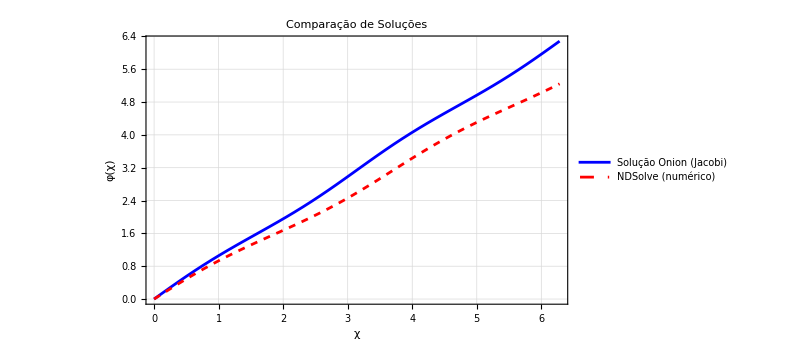

=== CÁLCULO DA ENERGIA ONION - Eq. (12) ===

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Energia Onion para diferentes ângulos ψ:

==========================================================================================

ψ (rad)	ψ (°)	k		K(k)		E(k)		W_on		E_on

==========================================================================================

0	0	0	π/2	π/2	-1	-0.0628

π/40	9/2	0.0783	1.5732	1.5684	0.0031	0.0001

π/20	9	0.1555	1.5804	1.5613	0.0124	0.0005

(3 π)/40	27/2	0.2303	1.5923	1.5498	0.0279	0.0012

π/10	18	0.3018	1.6085	1.5344	0.0499	0.0022

π/8	45/2	0.3691	1.6288	1.5159	0.0783	0.0035

(3 π)/20	27	0.4315	1.6527	1.4949	0.1136	0.0051

(7 π)/40	63/2	0.4886	1.6797	1.4724	0.1559	0.0071

π/5	36	0.5402	1.7091	1.4490	0.2055	0.0095

(9 π)/40	81/2	0.5862	1.7403	1.4256	0.2627	0.0123

π/4	45	0.6266	1.7725	1.4028	0.3280	0.0156

(11 π)/40	99/2	0.6618	1.8048	1.3812	0.4016	0.0194

(3 π)/10	54	0.6920	1.8365	1.3612	0.4839	0.0239

(13 π)/40	117/2	0.7175	1.8668	1.3432	0.5751	0.0291

(7 π)/20	63	0.7387	1.8948	1.3273	0.6755	0.0350

(3 π)/8	135/2	0.7559	1.9198	1.3138	0.7853	0.0418

(2 π)/5	72	0.7696	1.9413	1.3026	0.9044	0.0495

(17 π)/40	153/2	0.7799	1.9585	1.2940	1.0327	0.0583

(9 π)/20	81	0.7871	1.9712	1.2878	1.1699	0.0683

(19 π)/40	171/2	0.7913	1.9789	1.2841	1.3156	0.0796

π/2	90	0.7927	1.9815	1.2828	1.4691	Indeterminate

=== GRÁFICO W_on(ψ) - Reproduzindo Fig. 2(a) ===

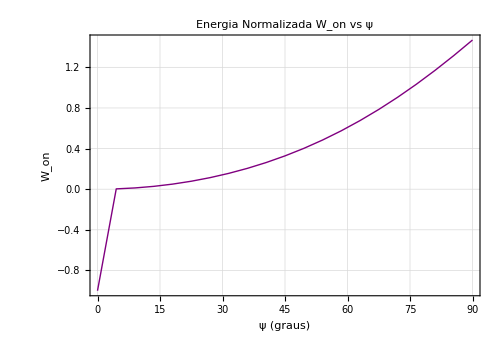

=== GRÁFICO E_on(ψ) ===

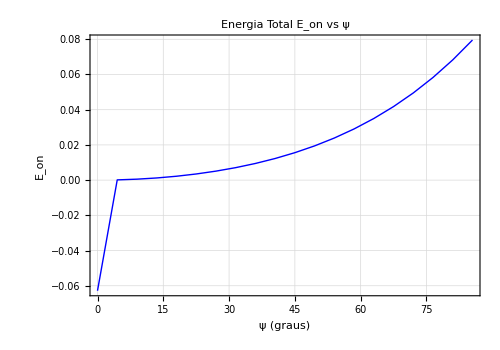

=== CASOS ESPECÍFICOS ===

1. ψ = 0 (Cilindro):

W_on = 5.×10^-7

E_on = 2.17759×10^-8

2. ψ = π/4 (Cone 45°):

k = 0.626647

K(k) = 1.77248

E(k) = 1.40284

W_on = 0.327997

E_on = 0.0155868

3. ψ = π/3 (Cone 60°):

k = 0.724982

K(k) = 1.87639

E(k) = 1.33764

W_on = 0.607536

E_on = 0.0309553

=== VERIFICAÇÃO: 2k*K(k) = π*sin(ψ) ===

Para ψ = π/4:

Lado esquerdo: 2k*K(k) = 2.22144

Lado direito: π*sin(ψ) = π/(√2)

Diferença = 8.88178×10^-16

=== PAINEL B: ψ = 0 ===

-Graphics3D-

=== PAINEL C: ψ = π/4 ===

-Graphics3D-

=== PAINEL C2: ψ = π/3 ===

-Graphics3D-

=== PAINEL D: Comparação mn(χ) ===

-Graphics-

=== PAINEL E: Plano de Corte ===

-Graphics-

=== FIGURA COMPLETA ===

-Graphics-

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D-MAGNETIZAÇÃO EM CONE*)(*Reproduzindo Gaididei 2014-FIG.1*)(*Incluindo ψ=0,π/4 e π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;        (*raio base*)
sigma=0.15;   (*parâmetro*)
w=1.0;        (*largura radial*)

(* =========================================*)
(*FUNÇÃO PRINCIPAL PARA PROCESSAR CONE*)
(* =========================================*)

ProcessCone3D[psiVal_]:=Module[{psi,k,kSol,phiOnion,dPhiOnionDchi,FtCone,mnNorm,mcn,xCone,yCone,zCone,chiGrid,rGrid,colorFunction,vectorField},psi=psiVal;
(*Parametrização 3D do cone*)xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];
(*Encontrar módulo k para solução onion*)If[Abs[psi]<0.001,kSol=0;
phiOnion[chiVal_]:=chiVal,kSol=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
phiOnion[chiVal_]:=JacobiAmplitude[(2*chiVal/Pi)*EllipticK[kSol^2],kSol^2]];
Print["  k = ",kSol//N];
(*Derivada numérica de phi*)dPhiOnionDchi[chiVal_]:=If[Abs[psi]<0.001,1,Derivative[1][phiOnion][chiVal]];
(*Campo efetivo Ft*)FtCone[phiVal_,dPhiDchiVal_,chiVal_,rVal_]:=Module[{g,term1,term2},g=(R+rVal*Cos[psi])^2;
term1=Sin[psi]*Sin[phiVal];
term2=2*dPhiDchiVal-Cos[psi];
term1*term2/Sqrt[g]];
(*Componente normal normalizada*)mcn=sigma^2/R^2;
mnNorm[chiVal_,rVal_]:=Module[{phiVal,dPhiVal,ftVal},phiVal=phiOnion[chiVal];
dPhiVal=dPhiOnionDchi[chiVal];
ftVal=FtCone[phiVal,dPhiVal,chiVal,rVal];
R^2*ftVal/mcn];
(*Grid para superfície*)chiGrid=Table[chi,{chi,0,2*Pi,2*Pi/50}];
rGrid=Table[r,{r,0.05,w,w/30}];
(*Criar função de cor baseada em posição*)colorFunction[x_,y_,z_]:=Module[{chi,r,mnVal},chi=Mod[ArcTan[x,y],2*Pi];
r=Sqrt[x^2+y^2]-R;
If[r<0.01,r=0.01];
If[r>w,r=w];
mnVal=mnNorm[chi,r];
ColorData["TemperatureMap"][Rescale[mnVal,{-0.75,0.75}]]];
(*Campo vetorial para streamlines*)vectorField=Table[Module[{phiVal,eChi,eR,mChi,mR,startPt,endPt,scale},phiVal=phiOnion[chi];
(*Vetores base tangente normalizados*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes de m*)mChi=Cos[phiVal];
mR=Sin[phiVal]*Cos[psi];
(*Ponto inicial e final*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];
{xCone,yCone,zCone,colorFunction,vectorField,mnNorm,phiOnion}]

(* =========================================*)
(*PANEL B:PSI=0 (CILINDRO)*)
(* =========================================*)

Print["Processando Painel B: ψ = 0..."];
{xB,yB,zB,colorB,vecB,mnB,phiB}=ProcessCone3D[0];

plotB=Show[ParametricPlot3D[{xB[chi,r],yB[chi,r],zB[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorB[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecB,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(b) ψ = 0",14,Bold]];

(* =========================================*)
(*PANEL C:PSI=π/4 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C: ψ = π/4..."];
{xC,yC,zC,colorC,vecC,mnC,phiC}=ProcessCone3D[Pi/4];

plotC=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c) ψ = π/4",14,Bold]];

(* =========================================*)
(*PANEL C2:PSI=π/3 (CONE)*)
(* =========================================*)

Print["\nProcessando Painel C2: ψ = π/3..."];
{xC2,yC2,zC2,colorC2,vecC2,mnC2,phiC2}=ProcessCone3D[Pi/3];

plotC2=Show[ParametricPlot3D[{xC2[chi,r],yC2[chi,r],zC2[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC2[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC2,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->350,PlotLabel->Style["(c2) ψ = π/3",14,Bold]];

(* =========================================*)
(*PANEL D:VARIAÇÃO mn(χ)-COMPARAÇÃO*)
(* =========================================*)

Print["\nProcessando Painel D: mn(χ) para diferentes ψ..."];

(*Dados para ψ=π/4*)
mnDataPi4={Table[{chi,mnC[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

(*Dados para ψ=π/3*)
mnDataPi3={Table[{chi,mnC2[chi,0.05]},{chi,0,2*Pi,2*Pi/200}],Table[{chi,mnC2[chi,R]},{chi,0,2*Pi,2*Pi/200}]};

Print["DEBUG - ψ = π/4:"];
Print["  r=0.05: Min = ",Min[mnDataPi4[[1,All,2]]],", Max = ",Max[mnDataPi4[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi4[[2,All,2]]],", Max = ",Max[mnDataPi4[[2,All,2]]]];

Print["DEBUG - ψ = π/3:"];
Print["  r=0.05: Min = ",Min[mnDataPi3[[1,All,2]]],", Max = ",Max[mnDataPi3[[1,All,2]]]];
Print["  r=R: Min = ",Min[mnDataPi3[[2,All,2]]],", Max = ",Max[mnDataPi3[[2,All,2]]]];

plotD=ListLinePlot[{mnDataPi4[[1]],mnDataPi4[[2]],mnDataPi3[[1]],mnDataPi3[[2]]},PlotStyle->{{Red,Thick},{Red,Dashed,Thick},{Blue,Thick},{Blue,Dashed,Thick}},PlotLegends->Placed[LineLegend[{"ψ=π/4, r=0","ψ=π/4, r=R","ψ=π/3, r=0","ψ=π/3, r=R"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.65,0.25}],Frame->True,FrameLabel->{Style["χ",14],Style["mn/m.b2cn",14]},PlotLabel->Style["(d) Comparação",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],PlotRange->{{0,2*Pi},{-0.7,0.7}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->500,AspectRatio->0.6];

(* =========================================*)
(*PANEL E:PLANO DE CORTE*)
(* =========================================*)

Print["\nProcessando Painel E: Plano de Corte..."];

plotE=Graphics[{(*Cone em corte*){LightGray,EdgeForm[{Black,Thick}],Polygon[{{-0.2,0},{-1.2,-0.7},{-1.2,0.7},{-0.2,0}}]},(*Vetores de magnetização m (laranja)*){Orange,Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z,phi,angle},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
phi=Pi/3;
angle=phi+t/3;
Arrow[{{y,z},{y+0.3*Cos[angle],z+0.3*Sin[angle]}}]],{t,-2*Pi/5,2*Pi/5,Pi/5}]},(*Vetores de campo Ft (verde)*){Darker[Green],Thickness[0.01],Arrowheads[0.05],Table[Module[{y,z},z=0.6*Sin[t];
y=-0.7-0.5*Cos[Pi/4]*(1-Cos[t]);
Arrow[{{y,z},{y-0.2,z+0.18*Sin[t]}}]],{t,-Pi/3,Pi/3,Pi/6}]},(*Labels*)Text[Style["m",16,Bold,Orange],{-0.4,0.6}],Text[Style["Ft",16,Bold,Darker[Green]],{-1.1,-0.4}],Text[Style["z",14],{0.1,0.9}],Text[Style["dy",14],{-1.3,0}],(*Eixos*){Black,Arrowheads[0.03],Arrow[{{-1.3,0},{0.2,0}}],Arrow[{{-0.2,-0.8},{-0.2,0.9}}]}},PlotLabel->Style["(e)",14,Bold],ImageSize->300,AspectRatio->1.2,PlotRange->{{-1.4,0.3},{-0.9,1}}];

(* =========================================*)
(*CÁLCULO DA ENERGIA E_t-VERSÃO COMPLETA*)
(*E_t=Γ.b2+(∇φ-Ω).b2*)
(*Incluindo AMBOS os termos do gradiente*)
(* =========================================*)

Print["\n=== CÁLCULO COMPLETO DA ENERGIA E_t ==="];
Print["Desenvolvimento: E_t = Γ.b2 + (∇φ - Ω).b2"];
Print["onde (∇φ).b2 = (∂φ/∂χ).b2/g₁₁ + (∂φ/∂r).b2/g₂₂"];

(*Para o cone com ψ=π/4*)
psi=Pi/4;

(*Calcular E_t COMPLETO para diferentes valores de chi e r*)
CalculateEtComplete[chi_,r_,phiVal_,dPhiDchi_,dPhiDr_]:=Module[{g11,g22,sqrtG,GammaChi,GammaR,Gamma2,gradPhiChi,gradPhiR,gradPhiSq,Omega1,Omega2,OmegaSq,crossTerm,Et,termBreakdown},(*Métrica*)g11=(R+r*Cos[psi])^2;
g22=1;
sqrtG=Sqrt[g11];
(*Componentes de Gamma (Eq.4)*)GammaChi=-Sin[psi]*Cos[phiVal]/sqrtG;
GammaR=0;
Gamma2=GammaChi^2+GammaR^2;
(*Gradiente COMPLETO de phi*)gradPhiChi=dPhiDchi/Sqrt[g11];
gradPhiR=dPhiDr/Sqrt[g22];
gradPhiSq=gradPhiChi^2+gradPhiR^2;
(*Spin connection Omega*)Omega1=-Sin[psi]/(R+r*Cos[psi]);
Omega2=0;
OmegaSq=Omega1^2+Omega2^2;
(*Termo cruzado:-2(∇φ)·Ω*)crossTerm=-2*(gradPhiChi*Omega1+gradPhiR*Omega2);
(*Energia total:E_t=Γ.b2+(∇φ).b2-2(∇φ)·Ω+Ω.b2*)Et=Gamma2+gradPhiSq+crossTerm+OmegaSq;
(*Retornar com decomposição*)termBreakdown={{"Γ.b2",Gamma2},{"(∇φ).b2",gradPhiSq},{"  ├─ (∂φ/∂χ).b2/g₁₁",gradPhiChi^2},{"  └─ (∂φ/∂r).b2/g₂₂",gradPhiR^2},{"-2(∇φ)·Ω",crossTerm},{"Ω.b2",OmegaSq},{"E_t TOTAL",Et}};
{Et,termBreakdown}];

(*Para solução onion:dphi/dr=0*)
Print["\n=== CASO 1: Solução Onion (∂φ/∂r = 0) ==="];

rValues={0.1,0.3,0.5,0.7,0.9};

Print["\nEm χ = π/2:"];
Print[StringRepeat["=",80]];

Do[Module[{chi,r,phiVal,dPhiVal,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
Print["\nr = ",N[r,3]];
Print[StringRepeat["-",80]];
Do[Print[StringForm["  `` = ``",result[[2,j,1]],NumberForm[N[result[[2,j,2]],6],{6,4}]]],{j,Length[result[[2]]]}];],{i,Length[rValues]}];

(*CASO 2:Testar com derivada radial não-nula*)
Print["\n\n=== CASO 2: Com ∂φ/∂r ≠ 0 (exemplo hipotético) ==="];
Print["Testando: ∂φ/∂r = 0.1 sin(χ)"];

Do[Module[{chi,r,phiVal,dPhiDchi,dPhiDr,result},chi=Pi/2;
r=rValues[[i]];
phiVal=phiC[chi];
dPhiDchi=Derivative[1][phiC][chi];
dPhiDr=0.1*Sin[chi];(*Exemplo de dependência radial*)result=CalculateEtComplete[chi,r,phiVal,dPhiDchi,dPhiDr];
Print["\nr = ",N[r,3]];
Print[StringRepeat["-",80]];
Do[Print[StringForm["  `` = ``",result[[2,j,1]],NumberForm[N[result[[2,j,2]],6],{6,4}]]],{j,Length[result[[2]]]}];],{i,Length[rValues]}];

(*Plotar E_t ao longo de chi para diferentes r-VERSÃO CORRIGIDA*)
EtDataMultiR=Table[Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,rVal,phiVal,dPhiVal,0];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/100}],{rVal,{0.1,0.3,0.5,0.7,0.9}}];

plotEtMultiR=ListLinePlot[EtDataMultiR,PlotStyle->{{Red,Thick},{Orange,Thick},{Green,Thick},{Blue,Thick},{Purple,Thick}},PlotLegends->Placed[LineLegend[{"r = 0.1","r = 0.3","r = 0.5","r = 0.7","r = 0.9"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.75,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(χ) para ψ = π/4 com diferentes r",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

(*Plotar E_t em função de r para chi fixo-VERSÃO CORRIGIDA*)
EtVsR=Table[Module[{chi,phiVal,dPhiVal,result},chi=Pi/2;
phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
{r,result[[1]]}],{r,0.05,0.95,0.01}];

plotEtVsR=ListLinePlot[EtVsR,PlotStyle->{Magenta,Thick},Frame->True,FrameLabel->{Style["r",14],Style["E_t",14]},PlotLabel->Style["Energia E_t(r) para ψ = π/4, χ = π/2",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

(*Mapa de densidade 2D:E_t(chi,r)-VERSÃO CORRIGIDA*)
EtMap2D=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,r,phiVal,dPhiVal,0];
result[[1]]],{chi,0,2*Pi,2*Pi/50},{r,0.05,0.95,0.02}];

plotEtMap=ListDensityPlot[Flatten[Table[{chi,r,EtMap2D[[i,j]]},{i,1,Length[EtMap2D]},{j,1,Length[EtMap2D[[1]]]}],1],ColorFunction->"Rainbow",PlotLegends->Automatic,Frame->True,FrameLabel->{Style["χ",14],Style["r",14]},PlotLabel->Style["Mapa 2D: E_t(χ, r) para ψ = π/4",14,Bold],InterpolationOrder->2,ImageSize->500,AspectRatio->0.6];

Print["\n=== GRÁFICO E_t(χ) PARA DIFERENTES r ==="];
Print[plotEtMultiR];

Print["\n=== GRÁFICO E_t(r) PARA χ = π/2 ==="];
Print[plotEtVsR];

Print["\n=== MAPA 2D DE E_t ==="];
Print[plotEtMap];

(* =========================================*)
(*IDENTIFICAR PONTOS CRÍTICOS DE ENERGIA*)
(* =========================================*)

Print["\n=== IDENTIFICAÇÃO DE PONTOS CRÍTICOS ==="];

(*Encontrar mínimos e máximos em função de chi para r fixo*)
rTest=0.5;
EtProfile=Table[Module[{phiVal,dPhiVal,result},phiVal=phiC[chi];
dPhiVal=Derivative[1][phiC][chi];
result=CalculateEtComplete[chi,rTest,phiVal,dPhiVal,0];
{chi,result[[1]]}],{chi,0,2*Pi,2*Pi/200}];

(*Encontrar posições de mínimos e máximos*)
etValues=EtProfile[[All,2]];
chiValues=EtProfile[[All,1]];

(*Buscar extremos locais*)
criticalPoints={};
Do[If[i>1&&i<Length[etValues],Module[{prev,curr,next},prev=etValues[[i-1]];
curr=etValues[[i]];
next=etValues[[i+1]];
(*Máximo local*)If[curr>prev&&curr>next,AppendTo[criticalPoints,{chiValues[[i]],curr,"Máximo"}]];
(*Mínimo local*)If[curr<prev&&curr<next,AppendTo[criticalPoints,{chiValues[[i]],curr,"Mínimo"}]];]],{i,2,Length[etValues]-1}];

Print["\nPontos críticos encontrados para r = ",rTest,":"];
Print[StringRepeat["=",80]];
Do[Print[StringForm["`` em χ = `` rad (``°), E_t = ``",criticalPoints[[i,3]],NumberForm[criticalPoints[[i,1]],{4,3}],NumberForm[criticalPoints[[i,1]]*180/Pi,{5,1}],NumberForm[criticalPoints[[i,2]],{6,4}]]],{i,Length[criticalPoints]}];

(*Converter para coordenadas 3D*)
criticalPoints3D=Table[Module[{chi,Et,tipo,x,y,z},chi=criticalPoints[[i,1]];
Et=criticalPoints[[i,2]];
tipo=criticalPoints[[i,3]];
x=xC[chi,rTest];
y=yC[chi,rTest];
z=zC[chi,rTest];
{{x,y,z},tipo,Et}],{i,Length[criticalPoints]}];

Print["\nCoordenadas 3D dos pontos críticos:"];
Do[Print[StringForm["`` em (x, y, z) = (`` , `` , ``), E_t = ``",criticalPoints3D[[i,2]],NumberForm[criticalPoints3D[[i,1,1]],{4,3}],NumberForm[criticalPoints3D[[i,1,2]],{4,3}],NumberForm[criticalPoints3D[[i,1,3]],{4,3}],NumberForm[criticalPoints3D[[i,3]],{6,4}]]],{i,Length[criticalPoints3D]}];

(*Plotar cone com pontos críticos marcados*)
plotConeWithCritical=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->True,AxesLabel->{"x","y","z"}],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vecC,1]}],(*Marcar mínimos em VERDE*)Graphics3D[{Green,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Mínimo"&]],(*Marcar máximos em VERMELHO*)Graphics3D[{Red,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Máximo"&]],(*Adicionar labels*)Graphics3D[Table[Text[Style[criticalPoints3D[[i,2]],12,Bold,If[criticalPoints3D[[i,2]]=="Mínimo",Green,Red]],criticalPoints3D[[i,1]]+{0,0,0.15}],{i,Length[criticalPoints3D]}]],ViewPoint->{2.5,-2,1.5},ImageSize->600,PlotLabel->Style["Cone com Pontos Críticos de Energia (ψ = π/4, r = 0.5)",14,Bold]];

Print["\n=== CONE 3D COM PONTOS CRÍTICOS MARCADOS ==="];
Print[plotConeWithCritical];

(*Plotar vista superior para melhor visualização*)
plotTopView=Show[ParametricPlot3D[{xC[chi,r],yC[chi,r],zC[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorC[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->True],Graphics3D[{Green,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Mínimo"&]],Graphics3D[{Red,Sphere[#[[1]],0.08]}&/@Select[criticalPoints3D,#[[2]]=="Máximo"&]],ViewPoint->{0,0,3},ImageSize->500,PlotLabel->Style["Vista Superior - Pontos Críticos",14,Bold]];

Print["\n=== VISTA SUPERIOR ==="];
Print[plotTopView];

(* =========================================*)
(*VERIFICAÇÃO:EQUAÇÃO DO PÊNDULO*)
(*φ''+(1/2)sin.b2ψ sin(2φ)=0*)
(* =========================================*)

Print["\n=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ==="];
Print["Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0"];

psiTest=Pi/4;

(*Calcular φ'' numericamente*)
chiTest=Table[chi,{chi,0,2*Pi,2*Pi/100}];
phiTest=Table[phiC[chi],{chi,chiTest}];

(*Derivadas numéricas*)
dPhi=Table[If[i<Length[phiTest],(phiTest[[i+1]]-phiTest[[i]])/(chiTest[[i+1]]-chiTest[[i]]),(phiTest[[i]]-phiTest[[i-1]])/(chiTest[[i]]-chiTest[[i-1]])],{i,Length[phiTest]}];

d2Phi=Table[If[i>1&&i<Length[dPhi],(dPhi[[i+1]]-dPhi[[i-1]])/(chiTest[[i+1]]-chiTest[[i-1]]),0],{i,Length[dPhi]}];

(*Termo do pêndulo*)
pendulumTerm=Table[0.5*Sin[psiTest]^2*Sin[2*phiTest[[i]]],{i,Length[phiTest]}];

(*Verificar equação:φ''+termo=0*)
residual=Table[d2Phi[[i]]+pendulumTerm[[i]],{i,Length[d2Phi]}];

(*Plotar verificação*)
plotPendulumCheck=ListLinePlot[{Table[{chiTest[[i]],d2Phi[[i]]},{i,2,Length[chiTest]-1}],Table[{chiTest[[i]],-pendulumTerm[[i]]},{i,2,Length[chiTest]-1}],Table[{chiTest[[i]],residual[[i]]},{i,2,Length[chiTest]-1}]},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick},{Green,Dotted,Thick}},PlotLegends->Placed[LineLegend[{"φ''(χ)","-(1/2)sin.b2ψ sin(2φ)","Resíduo"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.7,0.75}],Frame->True,FrameLabel->{Style["χ",14],Style["Valor",14]},PlotLabel->Style["Verificação: φ'' + (1/2)sin.b2ψ sin(2φ) = 0",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->600,AspectRatio->0.6];

Print["\n=== VERIFICAÇÃO DA EQUAÇÃO DO PÊNDULO ==="];
Print[plotPendulumCheck];

Print["\nEstatísticas do Resíduo:"];
Print["  RMS = ",Sqrt[Mean[residual[[2;;-2]]^2]]//N];
Print["  Max|resíduo| = ",Max[Abs[residual[[2;;-2]]]]//N];
Print["  (Valores próximos de zero indicam solução correta)"];

(* =========================================*)
(*RESOLVER EQUAÇÃO DO PÊNDULO DO ZERO*)
(* =========================================*)

Print["\n=== RESOLVER EQUAÇÃO DO PÊNDULO NUMERICAMENTE ==="];
Print["Equação: φ''(χ) + (1/2)sin.b2ψ sin(2φ) = 0"];
Print["Condições: φ(0) = 0, φ'(0) ≈ 1 (ajustado para periodicidade)"];

(*Sistema de EDO:y1=φ,y2=φ'*)
pendulumEq={y1'[chi]==y2[chi],y2'[chi]==-0.5*Sin[psiTest]^2*Sin[2*y1[chi]],y1[0]==0,y2[0]==1.0  (*Condição inicial para velocidade*)};

(*Resolver numericamente*)
solPendulum=NDSolve[pendulumEq,{y1,y2},{chi,0,2*Pi}];

phiNumerical[chi_]:=y1[chi]/. solPendulum[[1]];
dPhiNumerical[chi_]:=y2[chi]/. solPendulum[[1]];

(*Comparar com solução onion*)
plotComparison=Plot[{phiC[chi],phiNumerical[chi]},{chi,0,2*Pi},PlotStyle->{{Blue,Thick},{Red,Dashed,Thick}},PlotLegends->{"Solução Onion (Jacobi)","NDSolve (numérico)"},Frame->True,FrameLabel->{Style["χ",14],Style["φ(χ)",14]},PlotLabel->Style["Comparação de Soluções",14,Bold],GridLines->Automatic,ImageSize->600,AspectRatio->0.6];

Print["\n=== COMPARAÇÃO: ONION vs NUMÉRICO ==="];
Print[plotComparison];

(* =========================================*)
(*ENERGIA DA SOLUÇÃO ONION-Eq.(12)*)
(*E_on=E0(ψ)*W_on*)
(*W_on=1-sin.b2ψ/k.b2+4sinψ/π*E(k)/k-2cosψ*)
(* =========================================*)

Print["\n=== CÁLCULO DA ENERGIA ONION - Eq. (12) ==="];

(*Função para calcular energia onion*)
CalculateOnionEnergy[psiVal_,RVal_,wVal_,LVal_,lVal_]:=Module[{k,kVal,Kk,Ek,E0,Won,Eon},(*Encontrar módulo k:2k*K(k)=π*sin(ψ)*)If[Abs[psiVal]<0.001,kVal=0;
Kk=Pi/2;
Ek=Pi/2,kVal=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psiVal],{k,0.6}];
Kk=EllipticK[kVal^2];
Ek=EllipticE[kVal^2]];
(*E0(ψ)=2πLl.b2ln(1+w/R*cosψ)/cosψ*)If[Abs[psiVal]<0.001,E0=2*Pi*LVal*lVal^2*(wVal/RVal),(*Limite ψ->0*)E0=2*Pi*LVal*lVal^2*Log[1+wVal/RVal*Cos[psiVal]]/Cos[psiVal]];
(*W_on=1-sin.b2ψ/k.b2+4sinψ/(πk)*E(k)-2cosψ*)If[Abs[psiVal]<0.001,Won=1-2,(*Limite ψ->0:Won=-1*)Won=1-Sin[psiVal]^2/kVal^2+4*Sin[psiVal]/(Pi*kVal)*Ek-2*Cos[psiVal]];
(*Energia total*)Eon=E0*Won;
{Eon,E0,Won,kVal,Kk,Ek}];

(*Parâmetros físicos (unidades adimensionais)*)
LParam=1.0;   (*Comprimento característico*)
lParam=0.1;   (*Comprimento de troca*)
RParam=R;     (*Raio base*)
wParam=w;     (*Largura*)

(*Calcular energia para diferentes ψ*)
psiRange=Table[psi,{psi,0,Pi/2,Pi/40}];
onionEnergies=Table[CalculateOnionEnergy[psi,RParam,wParam,LParam,lParam],{psi,psiRange}];

Print["\nEnergia Onion para diferentes ângulos ψ:"];
Print[StringRepeat["=",90]];
Print["ψ (rad)\tψ (°)\tk\t\tK(k)\t\tE(k)\t\tW_on\t\tE_on"];
Print[StringRepeat["=",90]];

Do[Module[{psi,result},psi=psiRange[[i]];
result=onionEnergies[[i]];
Print[StringForm["``\t``\t``\t``\t``\t``\t``",NumberForm[psi,{4,3}],NumberForm[psi*180/Pi,{5,1}],NumberForm[result[[4]],{5,4}],NumberForm[result[[5]],{6,4}],NumberForm[result[[6]],{6,4}],NumberForm[result[[3]],{7,4}],NumberForm[result[[1]],{8,4}]]]],{i,Length[psiRange]}];

(*Plotar W_on vs ψ-Fig.2(a) do artigo*)
plotWon=ListLinePlot[Table[{psiRange[[i]]*180/Pi,onionEnergies[[i,3]]},{i,Length[psiRange]}],PlotStyle->{Purple,Thick},Frame->True,FrameLabel->{Style["ψ (graus)",14],Style["W_on",14]},PlotLabel->Style["Energia Normalizada W_on vs ψ",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

Print["\n=== GRÁFICO W_on(ψ) - Reproduzindo Fig. 2(a) ==="];
Print[plotWon];

(*Plotar E_on vs ψ*)
plotEon=ListLinePlot[Table[{psiRange[[i]]*180/Pi,onionEnergies[[i,1]]},{i,Length[psiRange]}],PlotStyle->{Blue,Thick},Frame->True,FrameLabel->{Style["ψ (graus)",14],Style["E_on",14]},PlotLabel->Style["Energia Total E_on vs ψ",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],ImageSize->500,AspectRatio->0.7];

Print["\n=== GRÁFICO E_on(ψ) ==="];
Print[plotEon];

(*Casos específicos*)
Print["\n=== CASOS ESPECÍFICOS ==="];

Print["\n1. ψ = 0 (Cilindro):"];
result0=CalculateOnionEnergy[0.001,RParam,wParam,LParam,lParam];
Print["   W_on = ",result0[[3]]];
Print["   E_on = ",result0[[1]]];

Print["\n2. ψ = π/4 (Cone 45°):"];
resultPi4=CalculateOnionEnergy[Pi/4,RParam,wParam,LParam,lParam];
Print["   k = ",resultPi4[[4]]];
Print["   K(k) = ",resultPi4[[5]]];
Print["   E(k) = ",resultPi4[[6]]];
Print["   W_on = ",resultPi4[[3]]];
Print["   E_on = ",resultPi4[[1]]];

Print["\n3. ψ = π/3 (Cone 60°):"];
resultPi3=CalculateOnionEnergy[Pi/3,RParam,wParam,LParam,lParam];
Print["   k = ",resultPi3[[4]]];
Print["   K(k) = ",resultPi3[[5]]];
Print["   E(k) = ",resultPi3[[6]]];
Print["   W_on = ",resultPi3[[3]]];
Print["   E_on = ",resultPi3[[1]]];

(*Verificar identidade:2k*K(k)=π*sin(ψ)*)
Print["\n=== VERIFICAÇÃO: 2k*K(k) = π*sin(ψ) ==="];
Print["Para ψ = π/4:"];
Print["   Lado esquerdo: 2k*K(k) = ",2*resultPi4[[4]]*resultPi4[[5]]];
Print["   Lado direito: π*sin(ψ) = ",Pi*Sin[Pi/4]];
Print["   Diferença = ",Abs[2*resultPi4[[4]]*resultPi4[[5]]-Pi*Sin[Pi/4]]];

Print["\n=== PAINEL B: ψ = 0 ==="];
Print[plotB];

Print["\n=== PAINEL C: ψ = π/4 ==="];
Print[plotC];

Print["\n=== PAINEL C2: ψ = π/3 ==="];
Print[plotC2];

Print["\n=== PAINEL D: Comparação mn(χ) ==="];
Print[plotD];

Print["\n=== PAINEL E: Plano de Corte ==="];
Print[plotE];

(*Grid final estilo artigo-3x2*)
finalFig=GraphicsGrid[{{plotB,plotC,plotC2},{plotD,plotE,SpanFromLeft}},ImageSize->1100,Spacings->{30,30}];

Print["\n=== FIGURA COMPLETA ==="];
Print[finalFig];
```

Encontrando angulo critico psi_c...

psi_c = 0.874113 rad

psi_c = 50.083 graus

psi_c/Pi = 0.278239 (teorico: 5/18 = 0.277778)

Won(psi_c) = 0.41175

Wax(psi_c) = 0.41175

Diferenca = 1.4988×10^-15

Calculando energias...

Gerando graficos...

=== PLOT A ===

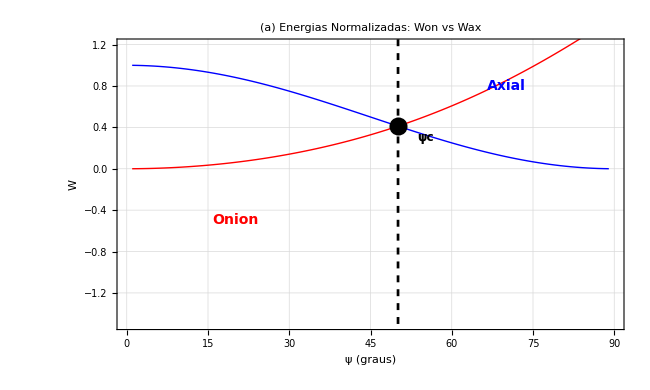

=== PLOT B ===

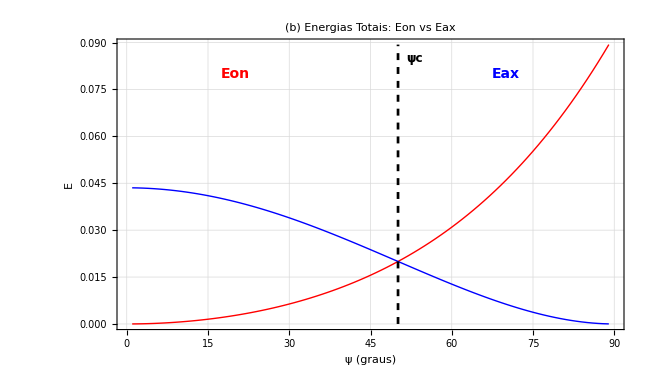

=== PLOT C ===

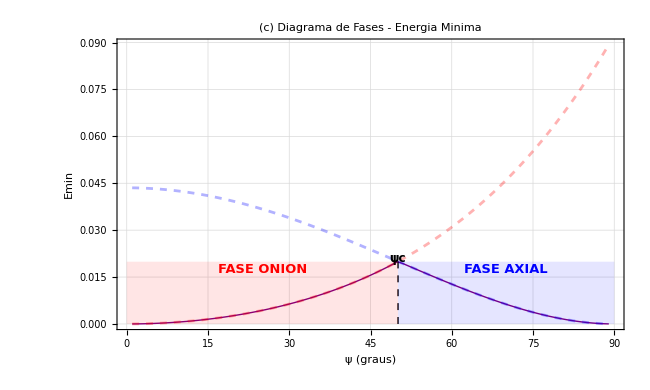

=== FIGURA COMPLETA ===

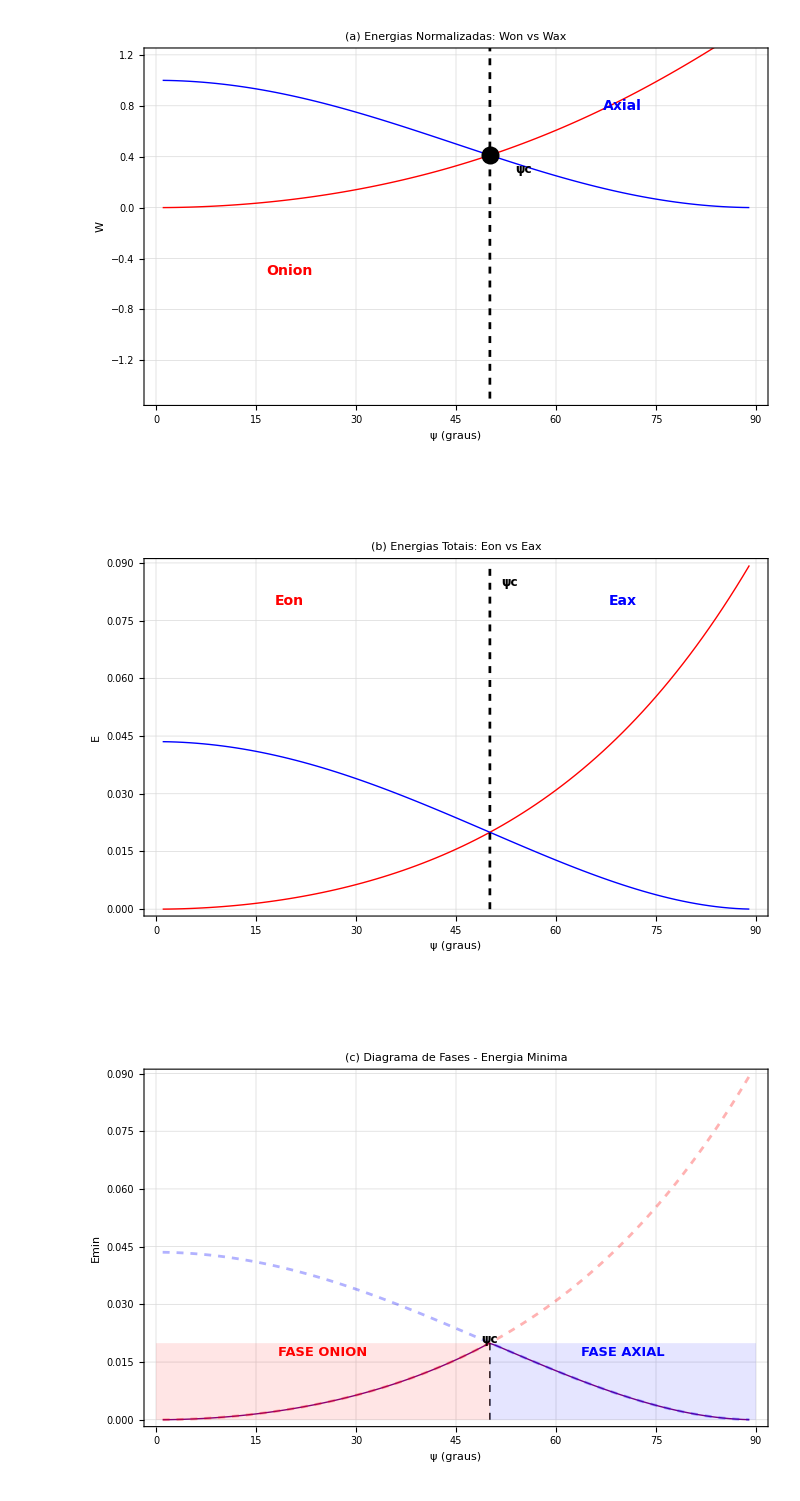

=== TABELA DE COMPARACAO ===

Psi(deg)  Won       Wax       Eon       Eax       Fase

=============================================================

5         0.004    Cos[π/36]^2       0.0002      0.0433   Onion

15         0.035    1/8 (      1+√3)^2       0.0015      0.0410   Onion

30         0.141    3/4       0.0064      0.0339   Onion

45         0.328    1/2       0.0156      0.0238   Onion

50         0.410    Sin[(2 π)/9]^2       0.0199      0.0200   Onion

55         0.503    Sin[(7 π)/36]^2       0.0250      0.0163   Axial

60         0.608    1/4       0.0310      0.0127   Axial

75         0.989    1/8 (     -1+√3)^2       0.0553      0.0037   Axial

85         1.299    Sin[π/36]^2       0.0783      0.0005   Axial

=== ANALISE COMPLETA ===

Para psi < psi_c: ONION e a fase estavel

Para psi > psi_c: AXIAL e a fase estavel

Em psi_c: TRANSICAO DE FASE de primeira ordem

```mathematica
(* =========================================*)(*COMPARAÇÃO:SOLUÇÕES ONION vs AXIAL*)(*Reproduzindo Fig.2 do artigo*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS FÍSICOS*)
(* =========================================*)

R=1.0;
w=1.0;
LParam=1.0;
lParam=0.1;

(* =========================================*)
(*E0(psi)*)
(* =========================================*)

E0Function[psiVal_?NumericQ]:=If[Abs[psiVal]<0.001,2*Pi*LParam*lParam^2*(w/R),2*Pi*LParam*lParam^2*Log[1+w/R*Cos[psiVal]]/Cos[psiVal]];

(* =========================================*)
(*Won(psi)-Energia normalizada Onion*)
(* =========================================*)

WonFunction[psiVal_?NumericQ]:=Module[{k,kVal,Kk,Ek,Won},If[Abs[psiVal]<0.001,Won=-1,kVal=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psiVal],{k,0.6}];
Ek=EllipticE[kVal^2];
Won=1-Sin[psiVal]^2/kVal^2+4*Sin[psiVal]/(Pi*kVal)*Ek-2*Cos[psiVal]];
Won];

(* =========================================*)
(*Wax(psi)-Energia normalizada Axial*)
(* =========================================*)

WaxFunction[psiVal_?NumericQ]:=Cos[psiVal]^2;

(* =========================================*)
(*ENCONTRAR ÂNGULO CRÍTICO*)
(* =========================================*)

Print["Encontrando angulo critico psi_c..."];

psiC=psi/. FindRoot[WonFunction[psi]-WaxFunction[psi]==0,{psi,0.87}];
WonC=WonFunction[psiC];
WaxC=WaxFunction[psiC];

Print["psi_c = ",N[psiC,6]," rad"];
Print["psi_c = ",N[psiC*180/Pi,4]," graus"];
Print["psi_c/Pi = ",N[psiC/Pi,6]," (teorico: 5/18 = ",N[5/18,6],")"];
Print["Won(psi_c) = ",N[WonC,6]];
Print["Wax(psi_c) = ",N[WaxC,6]];
Print["Diferenca = ",N[Abs[WonC-WaxC],8]];

(* =========================================*)
(*CALCULAR ENERGIAS PARA PLOTAGEM*)
(* =========================================*)

Print[""];
Print["Calculando energias..."];

psiDegrees=Range[1,89,1];
psiRadians=psiDegrees*Pi/180;

WonValues=Table[WonFunction[psi],{psi,psiRadians}];
WaxValues=Table[WaxFunction[psi],{psi,psiRadians}];

E0Values=Table[E0Function[psi],{psi,psiRadians}];
EonValues=E0Values*WonValues;
EaxValues=E0Values*WaxValues;

EminValues=Table[Min[EonValues[[i]],EaxValues[[i]]],{i,Length[EonValues]}];

(* =========================================*)
(*PLOT A:ENERGIAS NORMALIZADAS*)
(* =========================================*)

Print["Gerando graficos..."];

dataWon=Table[{psiDegrees[[i]],WonValues[[i]]},{i,Length[psiDegrees]}];
dataWax=Table[{psiDegrees[[i]],WaxValues[[i]]},{i,Length[psiDegrees]}];

plotA=Show[ListLinePlot[dataWon,PlotStyle->{Red,Thick}],ListLinePlot[dataWax,PlotStyle->{Blue,Thick}],Graphics[{Black,Dashed,Thickness[0.003],Line[{{psiC*180/Pi,-1.5},{psiC*180/Pi,1.5}}]}],Graphics[{Black,PointSize[0.02],Point[{psiC*180/Pi,WonC}]}],Graphics[{Text[Style["Onion",14,Bold,Red],{20,-0.5}],Text[Style["Axial",14,Bold,Blue],{70,0.8}],Text[Style["ψc",12,Bold],{psiC*180/Pi+5,0.3}]}],Frame->True,FrameLabel->{Style["ψ (graus)",14],Style["W",14]},PlotLabel->Style["(a) Energias Normalizadas: Won vs Wax",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]],PlotRange->{{0,90},{-1.5,1.2}},ImageSize->650,AspectRatio->0.6];

(* =========================================*)
(*PLOT B:ENERGIAS TOTAIS*)
(* =========================================*)

dataEon=Table[{psiDegrees[[i]],EonValues[[i]]},{i,Length[psiDegrees]}];
dataEax=Table[{psiDegrees[[i]],EaxValues[[i]]},{i,Length[psiDegrees]}];

plotB=Show[ListLinePlot[dataEon,PlotStyle->{Red,Thick}],ListLinePlot[dataEax,PlotStyle->{Blue,Thick}],Graphics[{Black,Dashed,Thickness[0.003],Line[{{psiC*180/Pi,0},{psiC*180/Pi,Max[EonValues]}}]}],Graphics[{Text[Style["Eon",14,Bold,Red],{20,0.08}],Text[Style["Eax",14,Bold,Blue],{70,0.08}],Text[Style["ψc",12,Bold],{psiC*180/Pi+3,Max[EonValues]*0.95}]}],Frame->True,FrameLabel->{Style["ψ (graus)",14],Style["E",14]},PlotLabel->Style["(b) Energias Totais: Eon vs Eax",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]],PlotRange->{{0,90},Automatic},ImageSize->650,AspectRatio->0.6];

(* =========================================*)
(*PLOT C:ENERGIA MÍNIMA (DIAGRAMA DE FASES)*)
(* =========================================*)

dataEmin=Table[{psiDegrees[[i]],EminValues[[i]]},{i,Length[psiDegrees]}];

plotC=Show[ListLinePlot[dataEmin,PlotStyle->{Purple,Thick}],ListLinePlot[dataEon,PlotStyle->{Red,Dashed,Opacity[0.3]}],ListLinePlot[dataEax,PlotStyle->{Blue,Dashed,Opacity[0.3]}],Graphics[{Black,Thick,Dashed,Line[{{psiC*180/Pi,0},{psiC*180/Pi,Max[EminValues]}}]}],Graphics[{Red,Opacity[0.1],Rectangle[{0,0},{psiC*180/Pi,Max[EminValues]}]}],Graphics[{Blue,Opacity[0.1],Rectangle[{psiC*180/Pi,0},{90,Max[EminValues]}]}],Graphics[{Text[Style["FASE ONION",13,Bold,Red],{25,Max[EminValues]*0.88}],Text[Style["FASE AXIAL",13,Bold,Blue],{70,Max[EminValues]*0.88}],Text[Style["ψc",12,Bold],{psiC*180/Pi,Max[EminValues]*1.05}]}],Frame->True,FrameLabel->{Style["ψ (graus)",14],Style["Emin",14]},PlotLabel->Style["(c) Diagrama de Fases - Energia Minima",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]],PlotRange->{{0,90},Automatic},ImageSize->650,AspectRatio->0.6];

(* =========================================*)
(*MOSTRAR GRÁFICOS*)
(* =========================================*)

Print[""];
Print["=== PLOT A ==="];
Print[plotA];

Print[""];
Print["=== PLOT B ==="];
Print[plotB];

Print[""];
Print["=== PLOT C ==="];
Print[plotC];

(* =========================================*)
(*GRID FINAL*)
(* =========================================*)

finalGrid=GraphicsGrid[{{plotA},{plotB},{plotC}},ImageSize->800,Spacings->{10,25}];

Print[""];
Print["=== FIGURA COMPLETA ==="];
Print[finalGrid];

(* =========================================*)
(*TABELA*)
(* =========================================*)

Print[""];
Print["=== TABELA DE COMPARACAO ==="];
Print["Psi(deg)  Won       Wax       Eon       Eax       Fase"];
Print["============================================================="];

selectedAngles={5,15,30,45,Round[psiC*180/Pi],55,60,75,85};

Do[Module[{idx,won,wax,eon,eax,phase},idx=Position[psiDegrees,Nearest[psiDegrees,ang][[1]]][[1,1]];
won=WonValues[[idx]];
wax=WaxValues[[idx]];
eon=EonValues[[idx]];
eax=EaxValues[[idx]];
phase=If[eon<eax,"Onion","Axial"];
Print[PaddedForm[ang,{3,0}],"      ",PaddedForm[won,{6,3}],"    ",PaddedForm[wax,{6,3}],"    ",PaddedForm[eon,{7,4}],"   ",PaddedForm[eax,{7,4}],"   ",phase]],{ang,selectedAngles}];

Print[""];
Print["=== ANALISE COMPLETA ==="];
Print["Para psi < psi_c: ONION e a fase estavel"];
Print["Para psi > psi_c: AXIAL e a fase estavel"];
Print["Em psi_c: TRANSICAO DE FASE de primeira ordem"];
```

Processando solucao ONION para psi = Pi/3...

k_onion = 0.724982

Processando solucao AXIAL para psi = Pi/3...

phi_axial = Pi/2 = 1.5708

m_chi = 0 (sem componente azimutal)

m_r = cos(psi) = 0.5

m_n = sin(psi) = 0.866025

Gerando grafico de phi(chi)...

=== COMPARACAO 3D: ONION vs AXIAL ===

-Graphics-

=== GRAFICO PHI(CHI) ===

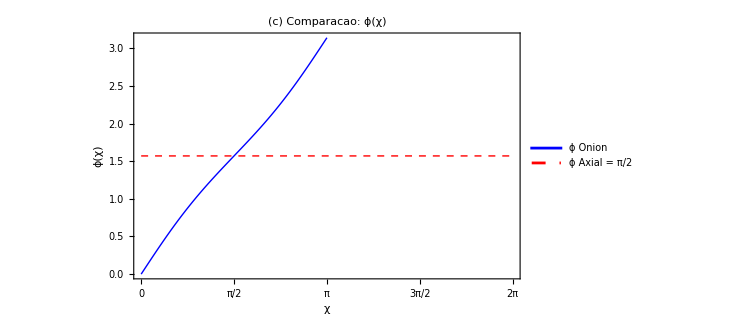

=== COMPONENTES DE MAGNETIZACAO ===

-Graphics-

=== FIGURA COMPLETA ===

=== ANALISE COMPARATIVA ===

SOLUCAO ONION (phi variavel):

- phi varia de 0 a 2K(k) ao longo de chi

- k = 0.724982

- m_chi = cos(phi) varia com chi

- m_r = sin(phi)cos(psi) varia com chi

- Topologia: vortice (winding number = 1)

SOLUCAO AXIAL (phi constante):

- phi = Pi/2 (constante)

- m_chi = 0 (sem componente azimutal)

- m_r = cos(psi) = 0.5 (constante)

- m_n = sin(psi) = 0.866025 (constante)

- Magnetizacao aponta na direcao radial

- Topologia: uniforme (winding number = 0)

PARA PSI = PI/3 = 60 graus:

- Fase estavel: AXIAL (psi > psi_c)

- Axial tem menor energia que Onion

```mathematica
(* =========================================*)(*VISUALIZAÇÃO 3D:SOLUÇÃO AXIAL NO CONE*)(*Comparando Onion vs Axial para ψ=π/3*)(* =========================================*)ClearAll["Global`*"]

(* =========================================*)
(*PARÂMETROS*)
(* =========================================*)

R=1.0;
sigma=0.15;
w=1.0;
psi=Pi/3;  (*ângulo do cone*)

(* =========================================*)
(*PARAMETRIZAÇÃO 3D DO CONE*)
(* =========================================*)

xCone[chi_,r_]:=(R+r*Cos[psi])*Cos[chi];
yCone[chi_,r_]:=(R+r*Cos[psi])*Sin[chi];
zCone[chi_,r_]:=r*Sin[psi];

(* =========================================*)
(*SOLUÇÃO ONION:φ=am(u|k)*)
(* =========================================*)

Print["Processando solucao ONION para psi = Pi/3..."];

(*Encontrar k:2k·K(k)=π·sin(ψ)*)
kOnion=k/. FindRoot[2*k*EllipticK[k^2]==Pi*Sin[psi],{k,0.6}];
Print["  k_onion = ",N[kOnion,6]];

(*Função phi onion*)
phiOnion[chi_]:=JacobiAmplitude[(2*chi/Pi)*EllipticK[kOnion^2],kOnion^2];

(*Componentes de magnetização Onion*)
(*m_chi=cos(φ),m_r=sin(φ)cos(ψ),m_n=sin(φ)sin(ψ)*)
mChiOnion[chi_,r_]:=Cos[phiOnion[chi]];
mROnion[chi_,r_]:=Sin[phiOnion[chi]]*Cos[psi];
mNOnion[chi_,r_]:=Sin[phiOnion[chi]]*Sin[psi];

(* =========================================*)
(*SOLUÇÃO AXIAL:φ=π/2 (constante)*)
(* =========================================*)

Print["Processando solucao AXIAL para psi = Pi/3..."];

phiAxial=Pi/2;

(*Componentes de magnetização Axial*)
(*m_chi=cos(π/2)=0,m_r=sin(π/2)cos(ψ)=cos(ψ),m_n=sin(π/2)sin(ψ)=sin(ψ)*)
mChiAxial[chi_,r_]:=0;
mRAxial[chi_,r_]:=Cos[psi];
mNAxial[chi_,r_]:=Sin[psi];

Print["  phi_axial = Pi/2 = ",N[Pi/2,6]];
Print["  m_chi = 0 (sem componente azimutal)"];
Print["  m_r = cos(psi) = ",N[Cos[psi],6]];
Print["  m_n = sin(psi) = ",N[Sin[psi],6]];

(* =========================================*)
(*CAMPO VETORIAL-ONION*)
(* =========================================*)

vectorFieldOnion=Table[Module[{phi,eChi,eR,mChi,mR,startPt,endPt,scale},phi=phiOnion[chi];
(*Vetores base tangente*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes*)mChi=Cos[phi];
mR=Sin[phi]*Cos[psi];
startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];

(* =========================================*)
(*CAMPO VETORIAL-AXIAL*)
(* =========================================*)

vectorFieldAxial=Table[Module[{eChi,eR,mChi,mR,startPt,endPt,scale},(*Para solução axial:φ=π/2*)(*Vetores base tangente*)eChi={-Sin[chi],Cos[chi],0};
eR={Cos[psi]*Cos[chi],Cos[psi]*Sin[chi],Sin[psi]};
(*Componentes axial*)mChi=0;(*sem componente azimutal*)mR=Cos[psi];(*constante em r*)startPt={xCone[chi,r],yCone[chi,r],zCone[chi,r]};
scale=0.12;
endPt=startPt+scale*(mChi*eChi+mR*eR);
{startPt,endPt}],{chi,0,2*Pi-0.1,2*Pi/18},{r,0.15,w-0.1,(w-0.15)/6}];

(* =========================================*)
(*FUNÇÃO DE COR BASEADA EM φ*)
(* =========================================*)

(*Para Onion:cor varia com chi*)
colorFunctionOnion[x_,y_,z_]:=Module[{chi,phi},chi=Mod[ArcTan[x,y],2*Pi];
phi=phiOnion[chi];
ColorData["TemperatureMap"][Rescale[phi,{0,Pi}]]];

(*Para Axial:cor uniforme (φ=π/2)*)
colorFunctionAxial[x_,y_,z_]:=ColorData["TemperatureMap"][0.5];  (*φ=π/2 está no meio*)

(* =========================================*)
(*PLOT ONION*)
(* =========================================*)

plotOnion=Show[ParametricPlot3D[{xCone[chi,r],yCone[chi,r],zCone[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorFunctionOnion[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Orange,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vectorFieldOnion,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->400,PlotLabel->Style["(a) ONION: ψ = π/3",14,Bold]];

(* =========================================*)
(*PLOT AXIAL*)
(* =========================================*)

plotAxial=Show[ParametricPlot3D[{xCone[chi,r],yCone[chi,r],zCone[chi,r]},{chi,0,2*Pi},{r,0.05,w},ColorFunction->Function[{x,y,z,chi,r},colorFunctionAxial[x,y,z]],ColorFunctionScaling->False,Mesh->None,PlotPoints->50,Lighting->"Neutral",Boxed->False,Axes->False],Graphics3D[{Red,Arrowheads[0.025],Thickness[0.006],Arrow/@Flatten[vectorFieldAxial,1]}],ViewPoint->{2.5,-2,1.5},ImageSize->400,PlotLabel->Style["(b) AXIAL: ψ = π/3",14,Bold]];

(* =========================================*)
(*GRÁFICO DE φ(χ)*)
(* =========================================*)

Print[""];
Print["Gerando grafico de phi(chi)..."];

chiRange=Table[chi,{chi,0,2*Pi,2*Pi/100}];
phiOnionData=Table[{chi,phiOnion[chi]},{chi,chiRange}];
phiAxialData=Table[{chi,Pi/2},{chi,chiRange}];

plotPhi=ListLinePlot[{phiOnionData,phiAxialData},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed}},PlotLegends->Placed[LineLegend[{"ϕ Onion","ϕ Axial = π/2"},LegendFunction->(Framed[#,RoundingRadius->5]&)],{0.7,0.3}],Frame->True,FrameLabel->{Style["χ",14],Style["ϕ(χ)",14]},PlotLabel->Style["(c) Comparacao: ϕ(χ)",14,Bold],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed,Opacity[0.3]],PlotRange->{{0,2*Pi},{0,Pi}},FrameTicks->{{Automatic,Automatic},{{{0,"0"},{Pi/2,"π/2"},{Pi,"π"},{3*Pi/2,"3π/2"},{2*Pi,"2π"}},Automatic}},ImageSize->550,AspectRatio->0.6];

(* =========================================*)
(*COMPONENTES DE MAGNETIZAÇÃO*)
(* =========================================*)

(*Para r=0.5*)
rTest=0.5;

mChiOnionData=Table[{chi,mChiOnion[chi,rTest]},{chi,chiRange}];
mChiAxialData=Table[{chi,mChiAxial[chi,rTest]},{chi,chiRange}];

mROnionData=Table[{chi,mROnion[chi,rTest]},{chi,chiRange}];
mRAxialData=Table[{chi,mRAxial[chi,rTest]},{chi,chiRange}];

plotComponents=GraphicsRow[{ListLinePlot[{mChiOnionData,mChiAxialData},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed}},PlotLegends->{"Onion","Axial"},Frame->True,FrameLabel->{"χ","mχ"},PlotLabel->Style["(d) Componente mχ",12,Bold],GridLines->Automatic,ImageSize->350,AspectRatio->0.7],ListLinePlot[{mROnionData,mRAxialData},PlotStyle->{{Blue,Thick},{Red,Thick,Dashed}},PlotLegends->{"Onion","Axial"},Frame->True,FrameLabel->{"χ","mr"},PlotLabel->Style["(e) Componente mr",12,Bold],GridLines->Automatic,ImageSize->350,AspectRatio->0.7]},Spacings->20];

(* =========================================*)
(*COMPARAÇÃO LADO A LADO*)
(* =========================================*)

Print[""];
Print["=== COMPARACAO 3D: ONION vs AXIAL ==="];

comparison3D=GraphicsRow[{plotOnion,plotAxial},Spacings->30];
Print[comparison3D];

Print[""];
Print["=== GRAFICO PHI(CHI) ==="];
Print[plotPhi];

Print[""];
Print["=== COMPONENTES DE MAGNETIZACAO ==="];
Print[plotComponents];

(* =========================================*)
(*GRID FINAL*)
(* =========================================*)

finalFigure=GraphicsGrid[{{plotOnion,plotAxial},{plotPhi,SpanFromLeft},{plotComponents,SpanFromLeft}},ImageSize->1000,Spacings->{20,20},Frame->All,FrameStyle->Directive[Gray,Thickness[2]]];

Print[""];
Print["=== FIGURA COMPLETA ==="];
Print[finalFigure];

(* =========================================*)
(*ANÁLISE COMPARATIVA*)
(* =========================================*)

Print[""];
Print["=== ANALISE COMPARATIVA ==="];
Print[""];
Print["SOLUCAO ONION (phi variavel):"];
Print["  - phi varia de 0 a 2K(k) ao longo de chi"];
Print["  - k = ",N[kOnion,6]];
Print["  - m_chi = cos(phi) varia com chi"];
Print["  - m_r = sin(phi)cos(psi) varia com chi"];
Print["  - Topologia: vortice (winding number = 1)"];
Print[""];
Print["SOLUCAO AXIAL (phi constante):"];
Print["  - phi = Pi/2 (constante)"];
Print["  - m_chi = 0 (sem componente azimutal)"];
Print["  - m_r = cos(psi) = ",N[Cos[psi],6]," (constante)"];
Print["  - m_n = sin(psi) = ",N[Sin[psi],6]," (constante)"];
Print["  - Magnetizacao aponta na direcao radial"];
Print["  - Topologia: uniforme (winding number = 0)"];
Print[""];
Print["PARA PSI = PI/3 = 60 graus:"];
Print["  - Fase estavel: AXIAL (psi > psi_c)"];
Print["  - Axial tem menor energia que Onion"];
```